# Colony Example

In this notebook, we will show how to setup the executable and the input files for the Colony software, and analyze the data. We implement a simplified version of the Ising model: a toggle switch regulatory network interfaced by two quorum sensing pathways.

### Notebook options to improve readability on git repository

```mathematica
SetOptions[InputNotebook[],PrivateNotebookOptions->{"FileOutlineCache"->False},TrackCellChangeTimes->False]
```

### Directories definition [need user input]

```mathematica
pathPrefix="/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony_build/Build_Qt4.8.6/Release";
(*Directory where to write the input files, usually where we run the Colony executable.*)
inputFileDirectory=pathPrefix;
(*Directory where to write the output files of the simulations.*)
outputDirectory=pathPrefix;
(*Directory of the Colony source code. Part of the C++ functions are written by this Mathematica notebook into this directory as cpp files.*)
sourceDirectory="/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony";

(*Check if the directories exist*)
If[!DirectoryQ[pathPrefix],Print["pathPrefix directory does not exist!"];];
If[!DirectoryQ[inputFileDirectory],Print["inputFileDirectory directory does not exist!"];];
If[!DirectoryQ[outputDirectory],Print["outputDirectory directory does not exist!"];];
If[!DirectoryQ[sourceDirectory],Print["sourceDirectory directory does not exist!"];];
```

### General mathematica definitions

#### Definition of font size and image size for graphs

```mathematica
(*Note: these are absolute values of reference for the font size and image size of all graphs in the notebook. They are meant to be used in all the graphs and can be multiplied by a custom coefficient.*)
fontsize=18;
imagesize=500;
fontFamily="Arial";
```

#### String representation of numbers

Several functions to convert numbers to string. In particular, the fixed scientific form is very useful for outputting numbers the same way the C++ program does. The converting methods already implemented in Mathematica, such as ScientificForm, do not give the desired output (try to output examples below).

```mathematica
latexnumber[x_,precision_Integer]:=ScientificForm[x,precision,NumberFormat->(ToString[#1<>"\\cdot "<>#2<>"^{"<>#3<>"}"]&)]
Print["latexnumber[1.3453*^6,4] = ",latexnumber[1.3453*^6,4]];

intstring[k_,digits_:3]:=StringDrop[ToString[PaddedForm[k,digits,NumberPadding->{"0",""}]],{1,1}];
Print["intstring[3,4] = ",intstring[3,4]];

numberString[x_,precision_,digits_]:=ToString[PaddedForm[x,{precision,digits},NumberPadding->{"","0"}]]
Print["numberString[1.54323,2,1] = ",numberString[1.54323,2,1]];
Print["numberString[100.0,3,0] = ",numberString[100.0,3,0]];
Print["numberString[100.456734523,5,6] = ",numberString[100.456734523,5,6]];

fixedScientificForm[number_,digitsToTheRightOfDecimalPoint_]:=ScientificForm[N[number,digitsToTheRightOfDecimalPoint+1],digitsToTheRightOfDecimalPoint+1,NumberFormat->((Row[{
If[StringLength[#1]==1,
#1<>"."<>StringJoin[Table["0",{digitsToTheRightOfDecimalPoint+2-StringLength[#1]-1+If[number<0,1,0]}]],
#1<>StringJoin[Table["0",{digitsToTheRightOfDecimalPoint+2-StringLength[#1]+If[number<0,1,0]}]]],
"e",
ToString[PaddedForm[If[ToExpression[#3]===Null,0,ToExpression[#3]],2,NumberPadding->{"0",""},SignPadding->True,NumberSigns->{"-","+"}]]}])&)];
Print["fixedScientificForm[0.012,3] = ",fixedScientificForm[0.012,3]];
Print["fixedScientificForm[-0.012,3] = ",fixedScientificForm[-0.012,3]];
Print["fixedScientificForm[0.0123456,3] = ",fixedScientificForm[0.0123456,3]];
Print["fixedScientificForm[-0.0123456,3] = ",fixedScientificForm[-0.0123456,3]];
Print["fixedScientificForm[300,3] = ",fixedScientificForm[300,3]];
Print["fixedScientificForm[5,3] = ",fixedScientificForm[5,3]];
Print["fixedScientificForm[1.,3] = ",fixedScientificForm[1.,3]];
Print["fixedScientificForm[0.,3] = ",fixedScientificForm[0.,3]];
Print["fixedScientificForm[0,3] = ",fixedScientificForm[0,3]];
```

latexnumber[1.3453*^6,4] = 1.345\cdot 10^{6}

intstring[3,4] = 0003

numberString[1.54323,2,1] = 1.5

numberString[100.0,3,0] = 100.

numberString[100.456734523,5,6] = 100.460000

fixedScientificForm[0.012,3] = 1.200e-02

fixedScientificForm[-0.012,3] = -1.200e-02

fixedScientificForm[0.0123456,3] = 1.235e-02

fixedScientificForm[-0.0123456,3] = -1.235e-02

fixedScientificForm[300,3] = 3.000e+02

fixedScientificForm[5,3] = 5.000e+00

fixedScientificForm[1.,3] = 1.000e+00

fixedScientificForm[0.,3] = 0.000e+00

fixedScientificForm[0,3] = 0.000e+00

#### Improved plot markers

These are just examples to be copy pasted in graphs. Improved plot markers of different shapes with a white background.

With dynamic color of the plot markers

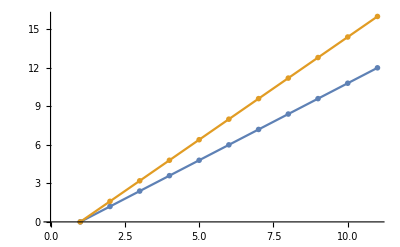

```mathematica
ListPlot[
{1.2Range[0,10,1],1.6Range[0,10,1]}
,Joined->True,
PlotMarkers:>{{
With[{plotMarkerThickness=0.1},
Graphics[{Dynamic@EdgeForm[{CurrentValue["Color"],Thickness[plotMarkerThickness]}],FaceForm[White],Disk[{0,0},1]},PlotRangePadding->Scaled[plotMarkerThickness/2]]
]
,0.05}}
]
```

Defining a list of plot styles for color of plot markers

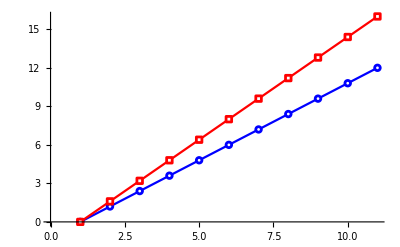

```mathematica
Module[{plotStyleList},
plotStyleList=Thread[{
{Disk[{0,0},1],Rectangle[]},
{Blue,Red}
}];
ListPlot[
{1.2Range[0,10,1],1.6Range[0,10,1]}
,Joined->True,
PlotStyle->(#[[2]]&/@plotStyleList),
PlotMarkers:>
({
With[{plotMarkerThickness=0.1},
Graphics[{EdgeForm[{#[[2]],Thickness[plotMarkerThickness]}],FaceForm[White],#[[1]]},PlotRangePadding->Scaled[plotMarkerThickness/2]]
]
,0.05}&/@plotStyleList)
]
]
```

#### Plot legend

Plots the legend inset.

```mathematica
legendPlottext[xl_List,colorlist_List:{},symbolList_List:{},graphSizeCoeff_:1,lineLength_:20,frameMargins_:5]:=Panel[Grid[MapIndexed[{
Graphics[
Flatten[{
If[colorlist=={},ColorData[1,First@#2],Extract[colorlist,First@#2]],
Thickness[0.1],Line[{{-1,0},{1,0}}],
If[symbolList=={},
{},
Inset[symbolList[[First@#2]],{0,0},{0,0},1*{1,1}]
]
}],ImageSize->{graphSizeCoeff*lineLength,Automatic},AspectRatio->1/1.2],
Style[#1,FontSize-> graphSizeCoeff*fontsize,FontFamily->fontFamily]}&,xl],
Alignment->{Left,Center},Spacings->graphSizeCoeff*{0.5,0.}],FrameMargins->graphSizeCoeff*frameMargins];
```

Simple example

```mathematica
legendPlottext[{xx,yy},{{Blue,Dashed,Dashing[{0.2,0.2}]},Red},{},2]
```

-Graphics- | xx
-Graphics- | yy

Example inset in a plot that has defined all the plot styles for the lines and plot markers

plotStyleList = {{Disk[{0,0},1],-Graphics-},{Rectangle[{-1,-1},{1,1}],-Graphics-}}

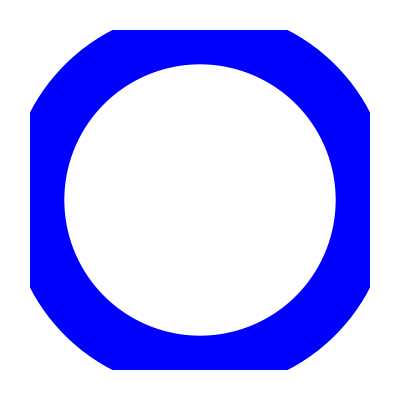
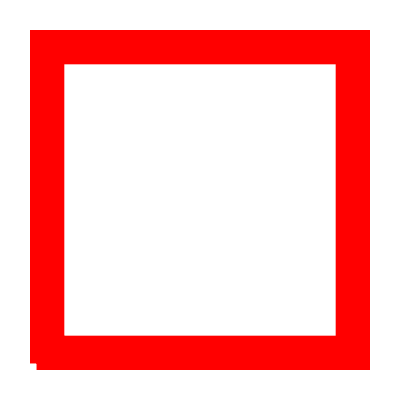
plotMarkerFunction/@plotStyleList = {-Graphics-,-Graphics-}

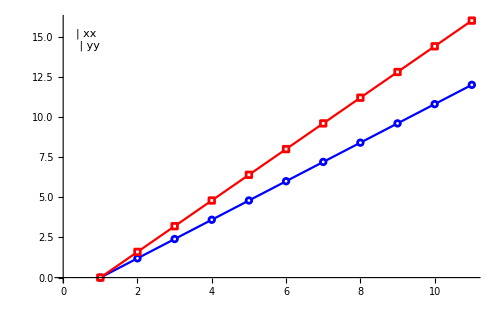

```mathematica
Module[{plotStyleList,plotMarkerFunction,graphSizeCoeff=1},

plotStyleList=Thread[{
{Disk[{0,0},1],Rectangle[{-1,-1},{1,1}]},
{Blue,Red}
}];
Print["plotStyleList = ",plotStyleList];

plotMarkerFunction=With[{plotMarkerThickness=0.1},
Graphics[{EdgeForm[{#[[2]],Thickness[plotMarkerThickness]}],FaceForm[White],#[[1]]},PlotRangePadding->Scaled[plotMarkerThickness/2]]
]&;
Print["plotMarkerFunction/@plotStyleList = ",plotMarkerFunction/@plotStyleList];

ListPlot[
{1.2Range[0,10,1],1.6Range[0,10,1]}
,Joined->True,
PlotStyle->(#[[2]]&/@plotStyleList),
PlotMarkers:>({#,0.04}&/@(plotMarkerFunction/@plotStyleList)),ImageSize->graphSizeCoeff*imagesize,
Epilog->Inset[legendPlottext[{"xx","yy"},plotStyleList[[All,2]],(plotMarkerFunction/@plotStyleList),graphSizeCoeff],Scaled[{0.05,0.95}],{Left,Top}]
]
]
```

#### Convert hexadecimal color from the web to decimal RGB color

```mathematica
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
hexToRGB["#FF8000"]
```

-Graphics-

## Definition of the system of reactions [need user input]

### Set cell growth, cell volume and area

First the total volume is determined based on the cell density and the number of cells.

```mathematica
Vtot=nCells/(nconc0(*cells/μm^3*))(*μm^3*);
```

Then the volume ratio Vx is determined based on Vtot, V0 and nCells, inverse of r.

```mathematica
Vx=(Vtot-nCells V0)/V0;
Vext=Vx V0;
```

Conversion coefficient molecules per cell -> nM

```mathematica
nmolesV0=(1*^9)/(6.02214*^23)  *1/(V0*1*^-15);
nmolesVext=(1*^9)/(6.02214*^23)  *1/(Vext*1*^-15);
```

V0 is replaced by the average of the cell volume over a cell cycle in the case of the exponential growth, V1=1/Log[2]V0, in order to compare correctly the deterministic model (with fixed cell volume) to the stochastic model (with dynamic growth).

```mathematica
nmolesV1=(1*^9)/(6.02214*^23)  *1/(V0/Log[2]*1*^-15);
(*For exponential growth, the phase corresponding to the average volume V1 is given by*)
phaseV1=N[-Log[Log[2]]/Log[2]];

(*Conversion function cell density cells/mL <--> number of cells*)
nconc[n_]:=n/(Vtot*1*^-12)/.par;(* n -> #cells/mL *)
concn[x_]:=(Vtot*1*^-12)*x/.par;(* #cells/mL -> n *)(* #cells/mL -> #cells*)
```

### List of species [need user input]

```mathematica
speciesCell={U,V,DNA,DNAboundToA,A,B};
speciesMilieu={Ue,Ve};

If[Length[Intersection[speciesCell,speciesMilieu]]≠0,Print["ERROR: the species cannot have the same name in the cell and in the milieu.",Intersection[speciesCell,speciesMilieu]];];
species=Join[speciesCell,speciesMilieu];
nSCell=Length[speciesCell];Print["Number of chemical species in 1 cell, nSCell = ",nSCell]
nSMilieu=Length[speciesMilieu];Print["Number of chemical species in the milieu, nSMilieu = ",nSMilieu]
S=nSCell+nSMilieu;Print["Total number of chemical species: S = ",S]
xCell=Table[speciesCell[[i]][t],{i,nSCell}]; Print["Table of species variables in the cell, xCell = ",xCell]
xMilieu=Table[speciesMilieu[[i]][t],{i,nSMilieu}]; Print["Table of species variables in the milieu, xMilieu = ",xMilieu]
x=Join[xCell,xMilieu]; Print["Table of species variables, x = ",x]
pos[s_,species_]:=Extract[Position[species,s],{1,1}] ;
pos[s_]:=pos[s,species];
Print["pos[x,speciesTable] gives the position of a species x in the speciesTable. Example: pos[Ve,species] = ",pos[Ve,species]]
```

Number of chemical species in 1 cell, nSCell = 6

Number of chemical species in the milieu, nSMilieu = 2

Total number of chemical species: S = 8

Table of species variables in the cell, xCell = {U[t],V[t],DNA[t],DNAboundToA[t],A[t],B[t]}

Table of species variables in the milieu, xMilieu = {Ue[t],Ve[t]}

Table of species variables, x = {U[t],V[t],DNA[t],DNAboundToA[t],A[t],B[t],Ue[t],Ve[t]}

pos[x,speciesTable] gives the position of a species x in the speciesTable. Example: pos[Ve,species] = 8

### Set of reactions [need user input]

Please keep the structure of the tables.
A reaction in the cell or in the milieu is written as a list:
{{reactants list},{products list},{1 if forward reaction is active 0 otherwise,1 if backward reaction is active 0 otherwise},{rate of forward reaction,rate of backward reaction}}
Note that the stochiometric coefficient has to be introduced by repeating the species name, as in {{U,U,U,V},{B},{1,1},{kf,kb}}.
The reactions of molecule transport accross the membrane (diffusion) can be written with the same syntax.

```mathematica
(*Note: the degradation rate is equal to unity.*)
reacCell={
{{},{U},{1,1},{α1+(β1 K1^3)/(K1^3+(V[t])^3),1}},
{{},{V},{1,1},{α2+(β2 K2^3)/(K2^3+(U[t])^3),1}},
{{},{A},{1,1},{kA,dA}},
{{DNA,A},{DNAboundToA},{1,1},{lAp,lAm}},
{{DNAboundToA},{DNAboundToA,B},{1,0},{kB,0}}
};

reacMilieu={
{{},{Ue},{1,0},{Uadded,0}},
{{Ue},{},{1,0},{1,0}},
{{Ve},{},{1,0},{1,0}}
};

reacCellMilieu={{{U}, {Ue}, {1,1}, {Dx,Dx}}, {{V}, {Ve}, {1,1}, {Dx,Dx}}};
reac=Join[reacCell,reacMilieu,reacCellMilieu];

nRCell=Length[reacCell];Print["Number of reactions in cell: ",nRCell]
nRMilieu=Length[reacMilieu];Print["Number of reactions in milieu: ",nRMilieu]
nRCellMilieu=Length[reacCellMilieu];Print["Number of reactions cell-milieu: ",nRCellMilieu]
R=Length[reac];Print["Number of total reactions: ",R]
dnaCell=Table[0,{nSCell},{nSCell}];
```

Number of reactions in cell: 5

Number of reactions in milieu: 3

Number of reactions cell-milieu: 2

Number of total reactions: 10

dnaCell is an array defining which species represent DNA molecule or DNA-bound complex.
 int array of size nSpecies x nSpecies.
This array defines which species are genetic material and which are
proteins.It is used to define which species are halved and which species
are copied during a division event.It is defined the following way :

On the diagonal, for i == j :
dnaSpecies_ (i, i) = 0 if species i is a protein = > will be halved during division event.
dnaSpecies_ (i, i) = 1 if species i is a protein - DNA complex = > will be unbound before division event.
dnaSpecies_ (i, i) = -1 if species i is a DNA molecule = > will be copied during division event.

In the bulk matrix, for i != j :
dnaSpecies_ (i, j) = n_ij if species i is a protein or a DNA molecule, then n_ij = 0 for all j.
                                         if species i is a protein - DNA complex, then n_ij define the stoichiometric vector of the unbounding reaction. In other words, it means that the protein - DNA complex is formed of :
n_i0*species0 + n_i1*species1 + ...

```mathematica
dnaCell=Table[0,{nSCell},{nSCell}];
```

```mathematica
dnaCell[[pos[DNA,speciesCell],pos[DNA,speciesCell]]]=-1;
dnaCell[[pos[DNAboundToA,speciesCell],pos[DNAboundToA,speciesCell]]]=1;
dnaCell[[pos[DNAboundToA,speciesCell],pos[DNA,speciesCell]]]=1;
dnaCell[[pos[DNAboundToA,speciesCell],pos[A,speciesCell]]]=1;
Print["dnaCell: ",dnaCell//MatrixForm]
```

dnaCell: (0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0
0 | 0 | 1 | 1 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0)

## Parameters [need user input]

### General parameters

```mathematica
par={
(*Reaction rates are defined in terms of concentration nM and dimensionless time units.*)
(*See above definition of the system of reaction for the meaning of the parameters*)
α2->α1,β2->β1,α1->1.0+γ,β1->15,Uadded->0,
K1->1*expressionLevel,K2->K1,expressionLevel->2.0,
Dx->2(*coefficient of diffusion*),
kA->1,dA->1,lAp->0.1,lAm->1,kB->10,
nCells->100(*initial number of cells in the colony*),
γ->N[Log[2]]/tau(*dilution simulating a chemostat*),
r->V0/Vext(*ratio of the initial volume of a cell at the beginning of cell cycle to the initial external volume*),
(*nconc0: initial cell density in cells/μm^3*)
(*Option 1: fixing the cell density*)
(*nconc0->1*^9(*cells/mL*)*1*^3(*cells/L*)*1*^-15(*cells/μm^3*),*)
(*Option 2: fixing the ratio rtot=nCells*Vcell/Vext*)
Solve[nCells/Vx==1,{nconc0}][[1,1]],
V0->1.5(*μm^3*)(*volume of the cell at the beginning of the cell cycle*),
L0->2.5,
r0->0.44,
cellLength0->2(*μm*)(*length of the cell at the beginning of the cell cycle*),
cellHeight0->1(*μm*)(*width of the cell at the beginning of the cell cycle*),
tau->50(*deterministic part of cell cycle duration*)
}
```

{α2→α1,β2→β1,α1→1.+γ,β1→15,Uadded→0,K1→expressionLevel,K2→K1,expressionLevel→2.,Dx→2,kA→1,dA→1,lAp→0.1,lAm→1,kB→10,nCells→100,γ→0.693147/tau,r→V0/(nCells/nconc0-nCells V0),nconc0→1/(2 V0),V0→1.5,L0→2.5,r0→0.44,cellLength0→2,cellHeight0→1,tau→50}

### Initial conditions and simulation parameters

In the following we define the initial conditions and the configuration file for the simulations.
In each simulation run, we can define a set of global parameters, let say {p_1,p_2,p_3} that we want to change in different simulation runs. These will be then treated as input parameters in the simulation and can have different values for each simulation run, for example changing the number of cells, a production rate, etc. Moreover, those global parameters that appear as coefficients in the reaction rates can also be changed during the timecourse of a simulation. For example, an exogenous inducer can be added at a fixed rate into the medium by defining the rate of its pseudo-reaction in the milieu as a pulse-like function with time. The time points when the value of {p_1,p_2,p_3} changes are defined in the table simTimePoints.The global parameters have a constant value inside each time interval, i.e. they follow a multiple steps function. Note that Length[simTimePoints] must be equal to Dimensions[globalParSet][[2]].

Example:

```mathematica
globalParList = {{p1}, {p2}};
simTimePoints = {10, 15, 50};
globalParSet = {{{5., 10.}, {6., 12.}, {7., 9.}}, {{3., 8.}, {3.2, 7.}, {3.5, 6.}}};
```

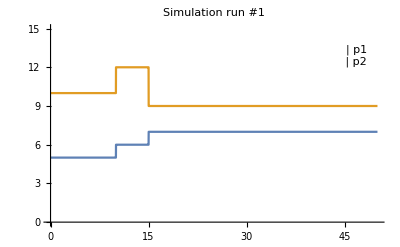

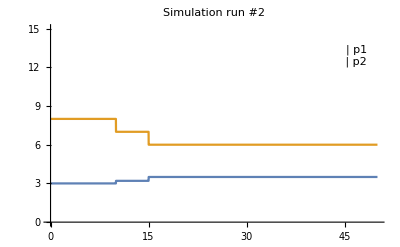

```mathematica
Plot[
{
Piecewise[{#[[1]],#[[2,1]]≤t<#[[2,2]]}&/@Thread[{globalParSet[[1,All,1]],Partition[Join[{0},simTimePoints],2,1]}]]/.t->t
,
Piecewise[{#[[1]],#[[2,1]]≤t<#[[2,2]]}&/@Thread[{globalParSet[[1,All,2]],Partition[Join[{0},simTimePoints],2,1]}]]/.t->t
},
{t,0,simTimePoints[[-1]]},PlotRange->{0,15},PlotLabel->"Simulation run #1",Epilog->Inset[legendPlottext[Flatten[globalParList]],Scaled[{0.95,0.9}],{Right,Top}]]
Plot[
{
Piecewise[{#[[1]],#[[2,1]]≤t<#[[2,2]]}&/@Thread[{globalParSet[[2,All,1]],Partition[Join[{0},simTimePoints],2,1]}]]/.t->t
,
Piecewise[{#[[1]],#[[2,1]]≤t<#[[2,2]]}&/@Thread[{globalParSet[[2,All,2]],Partition[Join[{0},simTimePoints],2,1]}]]/.t->t
},
{t,0,simTimePoints[[-1]]},PlotRange->{0,15},PlotLabel->"Simulation run #2",Epilog->Inset[legendPlottext[Flatten[globalParList]],Scaled[{0.95,0.9}],{Right,Top}]]
```

End of example

```mathematica
(*Choose algorithm.*)
algorithm="Langevin";
algorithm="Gillespie";
```

Define different set of initial conditions and time course of experiments.

Examples of experiments:
“Induction”: adding exogenous autoinducer U into the medium.
"Coupling": varying the diffusion coefficient for a fixed size colony.
“ExponentialGrowth”: simulating an exponentially growing colony.
“ExternalMagneticField”: varying the external field signal for a fixed sized colony.

```mathematica
experiment="Induction";
```

```mathematica
(*Default values for some simulation parameters (these may be changed below depending on the type of experiment).*)
x0CellDefault={1,5,1,0,0,0};
cellgrowth=False;
constantCellDensity=True;(*Keep the cell density constant (number of cells in the population).*)
stopWhenReachingMaximumVolume=True;
cellCycleDeterministic=tau//.par;
cellCycleGamma=0.8;
timeMeshSliceLength=1;(*Length of the time mesh intervals to record trajectories.*)
chemicalLangevinTimeStep=1*^-4;
changeTimeStepWithDiffusion=False;
nTimeStepsIntervalDisplaySimulationProgress=Round[10/timeMeshSliceLength];(*Display some simulation progress information in the standard output every n time steps.*)
spatialDynamicsEquilibrationTime=50;(*Presimulation time during which only the spatial movement of cells are computed, to start with a nicely packed colony. Only useful for movies.*)
firstPassageGFPThreshold=0;(*Threshold in concentration for computing first passage time.*)
computeSpatialDynamics=False;(*Compute spatial dynamics for making movie.*)
iseed=Random[Integer,1000000];(*Seed for random number generator.*)
Print["iseed = ",iseed];

Switch[experiment,
"Induction",
path=FileNameJoin[{outputDirectory,"Induction"}];
inputFilePath=FileNameJoin[{inputFileDirectory,"Induction"}];
,
"Coupling",
path=FileNameJoin[{outputDirectory,"Coupling"}];
inputFilePath=FileNameJoin[{inputFileDirectory,"Coupling"}];
,
"ExponentialGrowth",
path=FileNameJoin[{outputDirectory,"ExponentialGrowth"}];
inputFilePath=FileNameJoin[{inputFileDirectory,"ExponentialGrowth"}];
,
"ExternalMagneticField",
path=FileNameJoin[{outputDirectory,"ExternalMagneticField"}];
inputFilePath=FileNameJoin[{inputFileDirectory,"ExternalMagneticField"}];
];

Switch[algorithm,
"Langevin",
path=FileNameJoin[{path,"Langevin"}];
inputFilePath=FileNameJoin[{inputFilePath,"Langevin"}];
,
"Gillespie",
path=FileNameJoin[{path,"Gillespie"}];
inputFilePath=FileNameJoin[{inputFilePath,"Gillespie"}];
];



Switch[experiment,

"Induction"
,
(*Here we modify the par table to exclude the parameters that we want to change for the simulations.*)
par=Select[par,#[[1]]=!=Uadded&];

cellgrowth=True;
constantCellDensity=True;
simulationTime=400;
nTrajectories=1;

simTimePoints={simulationTime/2,(simulationTime/2)+10,simulationTime};
nTimeStepsIntervalDisplaySimulationProgress=Round[simulationTime/timeMeshSliceLength/100];
(*In globalParList only the name of the parameters is important*)
globalParList={{Uadded,0}};
(*In globalParSet are the values of the parameter sets.*)
globalParSet={{{0},{0},{0}},{{0},{100},{0}},{{0},{1000},{0}}};

(*Multithreading loop: write as many input files as number of threads.*)
nParameterPerThread=1;
multiThreadingGlobalParIndicesTable=Partition[Range[Length[globalParSet]],nParameterPerThread];

(*globalPar is the list of rules of replacement.*)
globalPar=#[[1]]->#[[2]]&/@globalParList;
nGlobalParSet=Dimensions[globalParSet][[1]];

x0CellHeterogeneous=False;(*different initial conditions for each cell in the colony*)
x0CellChangingWithGlobalPar=False;(*different initial conditions for each simulation run of parameter set*)
x0MilieuChangingWithGlobalPar=False;

,

"Coupling"
,
(*Here we modify the par table to exclude the parameters that we want to change for the simulations.*)
par=Select[par,#[[1]]=!=Dx&];

cellgrowth=False;
simulationTime=1000;
nTrajectories=1;
simTimePoints={simulationTime};

changeTimeStepWithDiffusion=True;(*Adjust the Langevin time step depending on the diffusion rate.*)
nTimeStepsIntervalDisplaySimulationProgress=Round[simulationTime/timeMeshSliceLength/100];

(*In globalParList only the name of the parameters is important*)
globalParList={{Dx,0}};
(*In globalParSet are the values of the parameter sets.*)
globalParSet=Partition[Partition[N[Join[{0.001,0.01,0.05},Range[0.1,0.4,0.1],Range[0.45,1.5,0.05],Range[1.6,4,0.2],{5,6,7,8,9,10}]],1],1];
globalParSet={{{0}},{{1*^-3}},{{1*^-2}},{{1*^-1}},{{1}},{{1*^1}},{{1*^2}},{{5*^2}},{{1*^3}},{{1*^4}}};

(*Multithreading. Here we split the different paremeters sets into small chunks that will be run by different threads. We write as many input files as number of threads.*)
nParameterPerThread=1;
multiThreadingGlobalParIndicesTable=Partition[Range[Length[globalParSet]],nParameterPerThread];

(*globalPar is the list of rules of replacement.*)
globalPar=#[[1]]->#[[2]]&/@globalParList;
nGlobalParSet=Dimensions[globalParSet][[1]];

x0CellHeterogeneous=True;(*different initial conditions for each cell in the colony*)
x0CellChangingWithGlobalPar=False;(*different initial conditions for each simulation run of parameter set*)
x0MilieuChangingWithGlobalPar=False;

,

"ExponentialGrowth"
,
(*Here we modify the par table to exclude the parameters that we want to change for the simulations.*)
par=Join[Select[par,#[[1]]=!=nCells&&#[[1]]=!=nconc0&&#[[1]]=!=tau&],{nCells->1,Solve[nCells/Vx==1/400,{nconc0}][[1,1]],tau->50}];

cellgrowth=True;
constantCellDensity=False;
simulationTime=N[Log[2,(400/nCells//.par)]]*tau//.par;
stopWhenReachingMaximumVolume=True;
timeMeshSliceLength=0.05;
cellCycleDeterministic=tau//.par;
spatialDynamicsEquilibrationTime=0;
computeSpatialDynamics=True;
firstPassageGFPThreshold=0;
nTrajectories=1;
changeTimeStepWithDiffusion=True;
simTimePoints={simulationTime};
nTimeStepsIntervalDisplaySimulationProgress=Round[simulationTime/timeMeshSliceLength/100];
(*In globalParList only the name of the parameters is important*)
globalParList={{Dx,0}};
(*In globalParSet are the values of the parameter sets.*)
globalParSet={{{2}}};


(*Multithreading loop: write as many input files as number of threads.*)
nParameterPerThread=1;
multiThreadingGlobalParIndicesTable=Partition[Range[Length[globalParSet]],nParameterPerThread];

(*globalPar is the list of rules of replacement.*)
globalPar=#[[1]]->#[[2]]&/@globalParList;
nGlobalParSet=Dimensions[globalParSet][[1]];

x0CellHeterogeneous=True;
x0CellChangingWithGlobalPar=False;
x0MilieuChangingWithGlobalPar=False;

,

"ExternalMagneticField"
,
(*Here we modify the par table to exclude the parameters that we want to change for the simulations.*)
par=Join[Select[par,#[[1]]=!=α1&&#[[1]]=!=α2&&#[[1]]=!=Dx&&#[[1]]=!=nCells&],{α1->αHzero+h,α2->αHzero,αHzero->α1/.par,Dx->1.0,nCells->10}];

cellgrowth=False;
simulationTime=10000;
timeMeshSliceLength=1;
nTrajectories=1;
changeTimeStepWithDiffusion=False;
simTimePoints={simulationTime};
nTimeStepsIntervalDisplaySimulationProgress=Round[simulationTime/timeMeshSliceLength/100];
(*In globalParList only the name of the parameters is important*)
globalParList={{h,0}};
(*In globalParSet are the values of the parameter sets.*)

(*Hysteresis simulation, we build a time mesh with h varying from -1 to +1 and back to -1 during the trajectory.*)
simTimePoints=N[Range[0,simulationTime,simulationTime/1000]];
globalParSet=
{
N[Partition[Join[Range[-1,1,2/((Length[simTimePoints]/2)-1)],Range[1,-1,-2/((Length[simTimePoints]/2)-1)],{-1}],1]]
};
Print["Length[simTimePoints] = ",Length[simTimePoints]," Length[globalParSet] = ",Length[globalParSet[[1]]]];

(*Multithreading loop: write as many input files as number of threads.*)
nParameterPerThread=1;
multiThreadingGlobalParIndicesTable=Partition[Range[Length[globalParSet]],nParameterPerThread];

(*globalPar is the list of rules of replacement.*)
globalPar=#[[1]]->#[[2]]&/@globalParList;
nGlobalParSet=Dimensions[globalParSet][[1]];

x0CellHeterogeneous=True;
x0CellChangingWithGlobalPar=False;
x0MilieuChangingWithGlobalPar=False;
]

(*Initial conditions in number of molecules.*)

x0HalfHalf=Join[
Table[Join[Round[{1,3}/nmolesV1]//.par,{1,0,0,0}],{Floor[(nCells//.par)/2]}],
Table[Join[Round[{3,1}/nmolesV1]//.par,{1,0,0,0}],{(nCells-Floor[nCells/2])//.par}]
];

If[x0CellChangingWithGlobalPar,
If[x0CellHeterogeneous
,
x0CellGeneralTable=Table[{
x0HalfHalf,
Table[CForm[phaseV1],{nCells//.par}]
},{iGlobalPar,nGlobalParSet}];
,
x0CellGeneralTable=Table[
Join[Round[{5,5}/nmolesV1],{1,0,0,0}]//.par
,{nGlobalParSet}];
];
,
If[x0CellHeterogeneous
,
x0CellHeterogeneousTable=x0HalfHalf;
phase0CellHeterogeneousTable=Table[CForm[phaseV1],{nCells//.par}];
x0CellGeneralTable={x0CellHeterogeneousTable,phase0CellHeterogeneousTable};
,
x0CellGeneralTable=Join[{1,1},{1,0,0,0}]//.par;
];
];

x0Milieu={0,0};
If[x0MilieuChangingWithGlobalPar,
x0MilieuGeneralTable=Table[Round[x0Milieu/nmolesVext],{i,nGlobalParSet}];
,
x0MilieuGeneralTable=Round[x0Milieu/nmolesVext];
];

outputPath=path;
inputFilePath=inputFilePath;

CreateDirectory[outputPath]
CreateDirectory[inputFilePath]

Print["x0Cell initial condition (nb of molecules) = ",x0CellGeneralTable];
Print["x0Milieu initial condition (nb of molecules) = ",x0MilieuGeneralTable];
Print["globalParSet = ",globalParSet];
Print["# globalParSet = ",nGlobalParSet];
Print["Output path = \n",outputPath];
Print["Input file path = \n",inputFilePath];
Print["Parameters = \n",par];
```

iseed = 684366

CreateDirectory::filex: "/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony_build/Build_Qt4.8.6/Release/Induction/Gillespie/" already exists.

/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony_build/Build_Qt4.8.6/Release/Induction/Gillespie

CreateDirectory::filex: "/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony_build/Build_Qt4.8.6/Release/Induction/Gillespie/" already exists.

/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony_build/Build_Qt4.8.6/Release/Induction/Gillespie

x0Cell initial condition (nb of molecules) = {1,1,1,0,0,0}

x0Milieu initial condition (nb of molecules) = {0,0}

globalParSet = {{{0},{0},{0}},{{0},{100},{0}},{{0},{1000},{0}}}

# globalParSet = 3

Output path = 
/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony_build/Build_Qt4.8.6/Release/Induction/Gillespie

Input file path = 
/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony_build/Build_Qt4.8.6/Release/Induction/Gillespie

Parameters = 
{α2→α1,β2→β1,α1→1.+γ,β1→15,K1→expressionLevel,K2→K1,expressionLevel→2.,Dx→2,kA→1,dA→1,lAp→0.1,lAm→1,kB→10,nCells→100,γ→0.693147/tau,r→V0/(nCells/nconc0-nCells V0),nconc0→1/(2 V0),V0→1.5,L0→2.5,r0→0.44,cellLength0→2,cellHeight0→1,tau→50}

## Deterministic equations and Langevin noise terms

### Reactions rates

Definition of the reactions rates for the deterministic approach and for the Gillespie stochastic approach.

kp=right and km=left reaction rates

For a spatially homogeneous mixture of chemical species, the microscopic rate of a chemical reaction depends on physical properties of the molecules and the temperature of the system, assumed constant. For a second-order reaction, A+B→E, the probability that a collision will occur in volume V(t) in the next infinitesimal time interval (t,t+dt) writes [1]
X_A X_B (V(t))^-1 π r_12^2 OverBar[v_12] dt.
At thermal equilibrium and if the collision has a probability p_12 of activating a reaction, the total reaction probability that a reaction will occur is
X_A X_B(V(t))^-1 π r_12^2 OverBar[v_12]  p_12 dt=X_A X_B c dt,
where
c=V(t)^-1 π r_12^2 OverBar[v_12] p_12 is called the stochastic reaction constant.
If we define
V(t)=V^*(t) V_0,
we can write the stochastic reaction constant as
c(t)=1/(V^*(t) V_0) π r_12^2 OverBar[v_12] p_12=1/(V^*(t))c_0 , where everything is constant and depends on physical properties of the system, except the volume which is variable.  Note that c_0 is adimensional.
The average number of molecules of E produced per unit of time is
X_E'(t)=X_A X_B c(t),
and the change in concentration in E (without considering the dilution term) is
(X_E'(t))/(V(t))=X_A/(V(t)) X_B c(t)=X_A/(V(t)) X_B/(V(t)) c(t)V(t)=c(t) V(t)c_A c_B.
The deterministic rate write
k=c(t) V(t) = c_0(V(t))/(V^*(t))=c_0 V_0,
and does not change with the volume. Herein we define the deterministic rates and derive the stochastic reaction constants, because the deterministic rates do not depend on the volume and are usually measured experimentally (contrary to the stochastic reaction constants). The derived stochastic reaction rate writes c_0=k/V_0=k*nmolesV0.

1. Gillespie D. Exact stochastic simulation of coupled chemical reactions. The journal of physical chemistry. 1977;81(25):2340–2361.

```mathematica
(*kp and km are the kinetic rates for the deterministic approach.*)
kpCell=Table[reacCell[[i,4,1]],{i,nRCell}];
kmCell=Table[reacCell[[i,4,2]],{i,nRCell}];
Print["kpCell: ",kpCell]
Print["kmCell: ",kmCell]

(*cp and cm are the rates of transition for the Gillespie algorithm*)
cpCell=Table[reacCell[[i,4,1]]*nmolesV0^(Length[reacCell[[i,1]]]-1),{i,nRCell}]/.Thread[x->x*nmolesV0];
cmCell=Table[reacCell[[i,4,2]]*nmolesV0^(Length[reacCell[[i,2]]]-1),{i,nRCell}]/.Thread[x->x*nmolesV0];
Print["cpCell: ",cpCell]
Print["cmCell: ",cmCell]

cpMilieu=Table[reacMilieu[[i,4,1]]*nmolesVext^(Length[reacMilieu[[i,1]]]-1),{i,nRMilieu}];
cmMilieu=Table[reacMilieu[[i,4,2]]*nmolesVext^(Length[reacMilieu[[i,2]]]-1),{i,nRMilieu}];
Print["cpMilieu: ",cpMilieu]
Print["cmMilieu: ",cmMilieu]
kpMilieu=Table[reacMilieu[[i,4,1]],{i,nRMilieu}];
kmMilieu=Table[reacMilieu[[i,4,2]],{i,nRMilieu}];
Print["kpMilieu: ",kpMilieu]
Print["kmMilieu: ",kmMilieu]

cpCellMilieu=Table[reacCellMilieu[[i,4,1]],{i,nRCellMilieu}];
cmCellMilieu=Table[reacCellMilieu[[i,4,2]],{i,nRCellMilieu}];
Print["cpCellMilieu: ",cpCellMilieu]
Print["cmCellMilieu: ",cmCellMilieu]

(*cp and cm are the rates of transition for the Gillespie algorithm*)
cp=Join[cpCell,cpMilieu,cpCellMilieu];
cm=Join[cmCell,cmMilieu,cmCellMilieu];
If[Length[cp]≠R||Length[cm]≠R,Print["Error: length of cp or cm is not equal to the number of reactions"]]

(*kp and km are the kinetic rates for the deterministic approach.*)
kp=reac[[All,4,1]];
km=reac[[All,4,2]];
Print["cp: ",cp]
Print["cm: ",cm]
Print["kp: ",kp]
Print["km: ",km]
```

kpCell: {α1+(K1^3 β1)/(K1^3+V[t]^3),α2+(K2^3 β2)/(K2^3+U[t]^3),kA,lAp,kB}

kmCell: {1,1,dA,lAm,0}

cpCell: {0.602214 V0 (α1+(K1^3 β1)/(K1^3+(4.57876 V[t]^3)/V0^3)),0.602214 V0 (α2+(K2^3 β2)/(K2^3+(4.57876 U[t]^3)/V0^3)),0.602214 kA V0,(1.66054 lAp)/V0,kB}

cmCell: {1,1,dA,lAm,0.}

cpMilieu: {0.602214 Uadded (nCells/nconc0-nCells V0),1,1}

cmMilieu: {0,0.,0.}

kpMilieu: {Uadded,1,1}

kmMilieu: {0,0,0}

cpCellMilieu: {Dx,Dx}

cmCellMilieu: {Dx,Dx}

cp: {0.602214 V0 (α1+(K1^3 β1)/(K1^3+(4.57876 V[t]^3)/V0^3)),0.602214 V0 (α2+(K2^3 β2)/(K2^3+(4.57876 U[t]^3)/V0^3)),0.602214 kA V0,(1.66054 lAp)/V0,kB,0.602214 Uadded (nCells/nconc0-nCells V0),1,1,Dx,Dx}

cm: {1,1,dA,lAm,0.,0,0.,0.,Dx,Dx}

kp: {α1+(K1^3 β1)/(K1^3+V[t]^3),α2+(K2^3 β2)/(K2^3+U[t]^3),kA,lAp,kB,Uadded,1,1,Dx,Dx}

km: {1,1,dA,lAm,0,0,0,0,Dx,Dx}

### Compute deterministic equations

#### Definition of reaction matrix

```mathematica
systemCell={speciesCell,nSCell,nRCell,reacCell,"Cell"};
systemMilieu={speciesMilieu,nSMilieu,nRMilieu,reacMilieu,"Milieu"};
systemTotal={species,S,R,reac,"Total"};

Do[
Module[{
species=system[[1]],
S=system[[2]],
R=system[[3]],
reac=system[[4]]},
NP1=Table[Table[Count[reac[[i]][[1]],species[[j]]],{j,1,S}],{i,1,R}];
NM1=Table[Table[Count[reac[[i]][[2]],species[[j]]],{j,1,S}],{i,1,R}];
NR1=NM1-NP1;
NV1=Join[NR1,-NR1];

If[system[[5]]=="Cell",NRCell=NR1;NVCell=NV1; NPCell=NP1; NMCell=NM1];
If[system[[5]]=="Milieu",NRMilieu=NR1;NVMilieu=NV1; NPMilieu=NP1; NMMilieu=NM1];
If[system[[5]]=="Total",NR=NR1;NV=NV1; NP=NP1; NM=NM1];

(*Print set of reactions*)
reacdiagram=Grid[Table[{i,Sum[NP1[[i]][[j]]species[[j]],{j,1,S}], If[Part[reac,i,3,1]==0&&Part[reac,i,3,2]≠0,"←",If[Part[reac,i,3,2]==0&&Part[reac,i,3,1]≠0,"→",If[Part[reac,i,3,2]≠0&&Part[reac,i,3,1]≠0,"⇄",If[Part[reac,i,3,2]==0&&Part[reac,i,3,1]==0,""]]]],Sum[NM1[[i]][[j]]species[[j]],{j,1,S}]},{i,1,R}],Alignment->{{Left,Right,Center,Left}}];

Clear[NP1,NM1,NR1,NV1];
]
,{system,{systemCell,systemMilieu,systemTotal}}];
Print[Style[reacdiagram,FontSize->16]];
Clear[systemCell,systemMilieu,systemTotal];

NPCellMilieu=
Table[
Table[Count[reacCellMilieu[[i,1]],species[[j]]],{j,1,S}]
,{i,nRCellMilieu}];
NMCellMilieu=
Table[
Table[Count[reacCellMilieu[[i,2]],species[[j]]],{j,1,S}]
,{i,nRCellMilieu}];
NRCellMilieu=NMCellMilieu-NPCellMilieu;
NVCellMilieu=Join[NRCellMilieu,-NRCellMilieu];
```

1 | 0 | ⇄ | U
2 | 0 | ⇄ | V
3 | 0 | ⇄ | A
4 | A+DNA | ⇄ | DNAboundToA
5 | DNAboundToA | → | B+DNAboundToA
6 | 0 | → | Ue
7 | Ue | → | 0
8 | Ve | → | 0
9 | U | ⇄ | Ue
10 | V | ⇄ | Ve

#### Compute deterministic equations

```mathematica
(*Define kinetic equations for each species*)
prod[x_]:=Product[x[[i]],{i,Length[x]}]/.Table[species[[i]]->species[[i]][t],{i,S}];
equfill=Table[0,{S}];
(*For each reaction, forward and backward, we fill the equations for corresponding involved species*)
Do[Do[
equfill[[i]]+=-Part[reac,j,3,1]NP[[j]][[i]]kp[[j]]prod[Part[reac,j,1]]+Part[reac,j,3,2]NP[[j]][[i]]km[[j]]prod[Part[reac,j,2]];
equfill[[i]]+=+Part[reac,j,3,1]NM[[j]][[i]]kp[[j]]prod[Part[reac,j,1]]-Part[reac,j,3,2]NM[[j]][[i]]km[[j]]prod[Part[reac,j,2]];
,{i,S}],{j,R}];
```

ADD DILUTION TERM :
All species inside the cell are being diluted at a rate -Log[2]/τ.
Note: As the noise terms will be computed based on the reaction matrix NV and the rate of reactions, not the deterministic equations, these additional dilution terms will not be included in the noise terms. We don’t want to include noise in the dilution process, we consider cell growth as a deterministic process (although the cell cycle duration can be stochastic).

```mathematica
If[cellgrowth,
Module[{splist,t1},
splist=pos/@Select[species,#=!=Ue&&#=!=Ve&];
Do[
equfill[[k]]+=-Log[2]/tau x[[k]];(*dilution term*)
,{k,splist}];
]
]
```

If[cellgrowth,Module[{splist,t1},splist=pos/@Select[species,#1=!=Ue&&#1=!=Ve&];Do[equfill⟦k⟧+=-(Log[2] x⟦k⟧)/tau;,{k,splist}];]]

VOLUME RATIO CORRECTION FOR DIFFUSION:
We multiply the reaction rate for the diffusion in the equation for the diffusing molecules in the milieu by the coefficient 1/Vnx, in order to satisfy mass conservation (the volumes for which concentrations of A and Aext are defined are different). Here Vnx is the ratio of the total volume to the volume of one cell. It depends on the cell density nconc0.

```mathematica
Module[{
listOfDiffusingChemicalSpeciesInMilieu=Union[Flatten[reacCellMilieu[[All,2]]]],
listOfDiffusionRatesChemicalSpeciesInMilieu=Union[Flatten[reacCellMilieu[[All,4,2]]]],
listRuleDiffusionRateVolumeCorrection
},
listRuleDiffusionRateVolumeCorrection=(#-># V0/Vext)&/@listOfDiffusionRatesChemicalSpeciesInMilieu;
Print["listRuleDiffusionRateVolumeCorrection = ",listRuleDiffusionRateVolumeCorrection];
Do[
Print["equation for ",u," before correction = ",equfill[[pos[u]]]];
equfill[[pos[u]]]=equfill[[pos[u]]]/.listRuleDiffusionRateVolumeCorrection;
Print["equation for ",u," after correction = ",equfill[[pos[u]]]];
,{u,listOfDiffusingChemicalSpeciesInMilieu}]
]
```

listRuleDiffusionRateVolumeCorrection = {Dx→(Dx V0)/(nCells/nconc0-nCells V0)}

equation for Ue before correction = Uadded+Dx U[t]-Ue[t]-Dx Ue[t]

equation for Ue after correction = Uadded+(Dx V0 U[t])/(nCells/nconc0-nCells V0)-Ue[t]-(Dx V0 Ue[t])/(nCells/nconc0-nCells V0)

equation for Ve before correction = Dx V[t]-Ve[t]-Dx Ve[t]

equation for Ve after correction = (Dx V0 V[t])/(nCells/nconc0-nCells V0)-Ve[t]-(Dx V0 Ve[t])/(nCells/nconc0-nCells V0)

WRITE EQUATIONS :

```mathematica
equ=Table[D[x[[i]],t]==equfill[[i]],{i,1,S}];

If[cellgrowth,equ2=equ;,equ1=equ;];
Style["Kinetic equations",FontSize->18]
If[!cellgrowth,Style[equ//TableForm,FontSize->18]]
If[cellgrowth,Style[equ//TableForm,FontSize->18]]
```

Kinetic equations

If[!cellgrowth,equ]

If[cellgrowth,equ]

### Compute the Langevin noise terms

Warning : computing the Langevin noise terms can be very computationally intensive even for reasonably small chemical reaction systems.

The chemical Langevin equation writes
(dX_i(t))/dt=∑_(j=1)^M ν_ji a_j(X(t))+∑_(j=1)^M ν_ji a_j^(1/2)(X(t))Γ_j(t)
where M is the number of reaction channels, ν_ij the change in number of species S_i molecules produced by one R_j reaction, a_j(X(t)) the propensity of reaction R_j and Γ_j(t) are temporally uncorrelated, statistically independent Gaussian white noises.

We can rewrite this Langevin equation into a standard-form Langevin equation,
(dX_i(t))/dt=A_i(X(t),t)+∑_(j=1)^M B_ij(X(t),t)Γ_j(t)
with
A_i(x,t)=∑_(j=1)^M ⋁_ji a_j(x)
B_ij(x,t)=⋁_ji a_j^(1/2)(x)
See this blog post for more details: http://www.marcweber.net/labnotebook/2015/11/06/multivariate-langevin-and-fokker-planck-equations/

We develop the terms aj for all the cells, from the definition of the reaction in 1 cell. We build a global system with the reactions in the following order:
Reactions table = [reactions in cell 1, ..., reactions in cell N, reactions in Milieu, reactions cell 1 <-> milieu, ..., reactions cell N <-> milieu].
Species table = [species in cell 1, ..., species in cell N, species in Milieu].

#### Compute the reaction rates aj

Here, aj depend on the deterministic rates and species concentrations.

```mathematica
aj=Module[{ajReacP,ajReacM,replaceVariablesByVariablesWithCellIndex},

replaceVariablesByVariablesWithCellIndex=Thread[x->species]/.Thread[species->Join[#[i][t]&/@speciesCell,#[t]&/@speciesMilieu]];

ajReacP=Table[reac[[j,3,1]]kp[[j]]Product[reac[[j,1,i]],{i,Length[reac[[j,1]]]}],{j,R}]/.Thread[x->species]/.Thread[species->Join[#[i][t]&/@speciesCell,#[t]&/@speciesMilieu]];
ajReacM=Table[reac[[j,3,2]]km[[j]]Product[reac[[j,2,i]],{i,Length[reac[[j,2]]]}],{j,R}]/.Thread[x->species]/.Thread[species->Join[#[i][t]&/@speciesCell,#[t]&/@speciesMilieu]];

Join[
Flatten[Table[ajReacP[[1;;nRCell]],{i,nCells/.par}]],
ajReacP[[nRCell+1;;nRCell+nRMilieu]],
Flatten[Table[ajReacP[[nRCell+nRMilieu+1;;-1]],{i,nCells/.par}]],
Flatten[Table[ajReacM[[1;;nRCell]],{i,nCells/.par}]],
ajReacM[[nRCell+1;;nRCell+nRMilieu]],
Flatten[Table[ajReacM[[nRCell+nRMilieu+1;;-1]],{i,nCells/.par}]]
]
];
```

```mathematica
aj
```

{α1+(K1^3 β1)/(K1^3+(V[1][t])^3),α2+(K2^3 β2)/(K2^3+(U[1][t])^3),kA,lAp A[1][t] DNA[1][t],kB DNAboundToA[1][t],α1+(K1^3 β1)/(K1^3+(V[2][t])^3),α2+(K2^3 β2)/(K2^3+(U[2][t])^3),kA,lAp A[2][t] DNA[2][t],kB DNAboundToA[2][t],α1+(K1^3 β1)/(K1^3+(V[3][t])^3),α2+(K2^3 β2)/(K2^3+(U[3][t])^3),kA,lAp A[3][t] DNA[3][t],kB DNAboundToA[3][t],1376,Dx Ve[t],Dx Ue[t],Dx Ve[t],Dx Ue[t],Dx Ve[t],Dx Ue[t],Dx Ve[t],Dx Ue[t],Dx Ve[t],Dx Ue[t],Dx Ve[t],Dx Ue[t],Dx Ve[t],Dx Ue[t],Dx Ve[t]}
 |  |  |  |

#### Build the NV reactions matrix for the complete nCells system

Here we build the reactions matrix NV for the complete system of N cells with diffusion reactions.

```mathematica
NVLangevin=Table[0,{2*((nRCell+nRCellMilieu)*nCells+nRMilieu)/.par},{(nSCell*nCells+nSMilieu)/.par}];
Module[{nCells1=nCells/.par},

Do[
NVLangevin[[(iCell-1)*nRCell+1;;iCell*nRCell,
(iCell-1)*nSCell+1;;iCell*nSCell]]
=NRCell;
,{iCell,nCells1}];

NVLangevin[[nCells1*nRCell+1;;nCells1*nRCell+nRMilieu,
nCells1*nSCell+1;;nCells1*nSCell+nSMilieu]]
=NRMilieu;

Do[

NVLangevin[[
nCells1*nRCell+nRMilieu+(iCell-1)*nRCellMilieu+1;;nCells1*nRCell+nRMilieu+iCell*nRCellMilieu
,
Join[(*Indices of species in cell i*)Range[(iCell-1)*nSCell+1,iCell*nSCell]
,(*Indices of species in milieu*)Range[nCells1*nSCell+1,nCells1*nSCell+nSMilieu]]
]]=NRCellMilieu;

,{iCell,nCells1}];

NVLangevin[[nCells1*nRCell+nRMilieu+nCells1*nRCellMilieu+1;;-1]]=-NVLangevin[[1;;nCells1*nRCell+nRMilieu+nCells1*nRCellMilieu]];
];
```

```mathematica
NVLangevin
```

{1}
 |  |  |  |

#### Build the noise terms matrix Bnoise

```mathematica
Bnoise=Table[
NVLangevin[[k,i]]Sqrt[aj[[k]]]
,{i,(nCells/.par)*nSCell+nSMilieu}
,{k,2*((nCells/.par)*nRCell+nRMilieu+(nCells/.par)*nRCellMilieu)}
];
G=Bnoise.Transpose[Bnoise];
```

$Aborted

Volume correction of the diffusion reactions

```mathematica
Module[{
listOfDiffusingChemicalSpeciesInMilieu=Union[Flatten[reacCellMilieu[[All,2]]]],
listOfDiffusionRatesChemicalSpeciesInMilieu=Union[Flatten[reacCellMilieu[[All,4,2]]]],
listRuleDiffusionRateVolumeCorrection
},
listRuleDiffusionRateVolumeCorrection=(#-># 1/Vx)&/@listOfDiffusionRatesChemicalSpeciesInMilieu;
Print["listRuleDiffusionRateVolumeCorrection = ",listRuleDiffusionRateVolumeCorrection];
Do[
Print["Bnoise for ",u," before correction = ",Bnoise[[(nCells/.par)*nSCell+pos[u,speciesMilieu]]]];
Bnoise[[(nCells/.par)*nSCell+pos[u,speciesMilieu]]]=Bnoise[[(nCells/.par)*nSCell+pos[u,speciesMilieu]]]/.listRuleDiffusionRateVolumeCorrection;
Print["Bnoise for ",u," after correction = ",Bnoise[[(nCells/.par)*nSCell+pos[u,speciesMilieu]]]];
,{u,listOfDiffusingChemicalSpeciesInMilieu}]
]
```

listRuleDiffusionRateVolumeCorrection = {Dx→(Dx V0)/(nCells/nconc0-nCells V0)}

Bnoise for Ue before correction = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,√Uadded,-√Ue[t],0,√(Dx U[1][t]),0,√(Dx U[2][t]),0,√(Dx U[3][t]),0,√(Dx U[4][t]),0,√(Dx U[5][t]),0,√(Dx U[6][t]),0,√(Dx U[7][t]),0,√(Dx U[8][t]),0,√(Dx U[9][t]),0,√(Dx U[10][t]),0,√(Dx U[11][t]),0,√(Dx U[12][t]),0,√(Dx U[13][t]),0,√(Dx U[14][t]),0,√(Dx U[15][t]),0,√(Dx U[16][t]),0,√(Dx U[17][t]),0,√(Dx U[18][t]),0,√(Dx U[19][t]),0,√(Dx U[20][t]),0,√(Dx U[21][t]),0,√(Dx U[22][t]),0,√(Dx U[23][t]),0,√(Dx U[24][t]),0,√(Dx U[25][t]),0,√(Dx U[26][t]),0,√(Dx U[27][t]),0,√(Dx U[28][t]),0,√(Dx U[29][t]),0,√(Dx U[30][t]),0,√(Dx U[31][t]),0,√(Dx U[32][t]),0,√(Dx U[33][t]),0,√(Dx U[34][t]),0,√(Dx U[35][t]),0,√(Dx U[36][t]),0,√(Dx U[37][t]),0,√(Dx U[38][t]),0,√(Dx U[39][t]),0,√(Dx U[40][t]),0,√(Dx U[41][t]),0,√(Dx U[42][t]),0,√(Dx U[43][t]),0,√(Dx U[44][t]),0,√(Dx U[45][t]),0,√(Dx U[46][t]),0,√(Dx U[47][t]),0,√(Dx U[48][t]),0,√(Dx U[49][t]),0,√(Dx U[50][t]),0,√(Dx U[51][t]),0,√(Dx U[52][t]),0,√(Dx U[53][t]),0,√(Dx U[54][t]),0,√(Dx U[55][t]),0,√(Dx U[56][t]),0,√(Dx U[57][t]),0,√(Dx U[58][t]),0,√(Dx U[59][t]),0,√(Dx U[60][t]),0,√(Dx U[61][t]),0,√(Dx U[62][t]),0,√(Dx U[63][t]),0,√(Dx U[64][t]),0,√(Dx U[65][t]),0,√(Dx U[66][t]),0,√(Dx U[67][t]),0,√(Dx U[68][t]),0,√(Dx U[69][t]),0,√(Dx U[70][t]),0,√(Dx U[71][t]),0,√(Dx U[72][t]),0,√(Dx U[73][t]),0,√(Dx U[74][t]),0,√(Dx U[75][t]),0,√(Dx U[76][t]),0,√(Dx U[77][t]),0,√(Dx U[78][t]),0,√(Dx U[79][t]),0,√(Dx U[80][t]),0,√(Dx U[81][t]),0,√(Dx U[82][t]),0,√(Dx U[83][t]),0,√(Dx U[84][t]),0,√(Dx U[85][t]),0,√(Dx U[86][t]),0,√(Dx U[87][t]),0,√(Dx U[88][t]),0,√(Dx U[89][t]),0,√(Dx U[90][t]),0,√(Dx U[91][t]),0,√(Dx U[92][t]),0,√(Dx U[93][t]),0,√(Dx U[94][t]),0,√(Dx U[95][t]),0,√(Dx U[96][t]),0,√(Dx U[97][t]),0,√(Dx U[98][t]),0,√(Dx U[99][t]),0,√(Dx U[100][t]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0,-√(Dx Ue[t]),0}

Bnoise for Ue after correction = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,√Uadded,-√Ue[t],0,√((Dx V0 U[1][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[2][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[3][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[4][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[5][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[6][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[7][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[8][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[9][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[10][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[11][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[12][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[13][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[14][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[15][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[16][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[17][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[18][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[19][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[20][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[21][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[22][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[23][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[24][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[25][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[26][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[27][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[28][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[29][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[30][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[31][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[32][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[33][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[34][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[35][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[36][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[37][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[38][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[39][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[40][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[41][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[42][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[43][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[44][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[45][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[46][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[47][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[48][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[49][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[50][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[51][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[52][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[53][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[54][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[55][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[56][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[57][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[58][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[59][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[60][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[61][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[62][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[63][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[64][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[65][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[66][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[67][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[68][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[69][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[70][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[71][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[72][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[73][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[74][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[75][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[76][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[77][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[78][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[79][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[80][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[81][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[82][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[83][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[84][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[85][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[86][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[87][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[88][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[89][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[90][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[91][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[92][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[93][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[94][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[95][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[96][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[97][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[98][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[99][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 U[100][t])/(nCells/nconc0-nCells V0)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ue[t])/(nCells/nconc0-nCells V0)),0}

Bnoise for Ve before correction = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-√Ve[t],0,√(Dx V[1][t]),0,√(Dx V[2][t]),0,√(Dx V[3][t]),0,√(Dx V[4][t]),0,√(Dx V[5][t]),0,√(Dx V[6][t]),0,√(Dx V[7][t]),0,√(Dx V[8][t]),0,√(Dx V[9][t]),0,√(Dx V[10][t]),0,√(Dx V[11][t]),0,√(Dx V[12][t]),0,√(Dx V[13][t]),0,√(Dx V[14][t]),0,√(Dx V[15][t]),0,√(Dx V[16][t]),0,√(Dx V[17][t]),0,√(Dx V[18][t]),0,√(Dx V[19][t]),0,√(Dx V[20][t]),0,√(Dx V[21][t]),0,√(Dx V[22][t]),0,√(Dx V[23][t]),0,√(Dx V[24][t]),0,√(Dx V[25][t]),0,√(Dx V[26][t]),0,√(Dx V[27][t]),0,√(Dx V[28][t]),0,√(Dx V[29][t]),0,√(Dx V[30][t]),0,√(Dx V[31][t]),0,√(Dx V[32][t]),0,√(Dx V[33][t]),0,√(Dx V[34][t]),0,√(Dx V[35][t]),0,√(Dx V[36][t]),0,√(Dx V[37][t]),0,√(Dx V[38][t]),0,√(Dx V[39][t]),0,√(Dx V[40][t]),0,√(Dx V[41][t]),0,√(Dx V[42][t]),0,√(Dx V[43][t]),0,√(Dx V[44][t]),0,√(Dx V[45][t]),0,√(Dx V[46][t]),0,√(Dx V[47][t]),0,√(Dx V[48][t]),0,√(Dx V[49][t]),0,√(Dx V[50][t]),0,√(Dx V[51][t]),0,√(Dx V[52][t]),0,√(Dx V[53][t]),0,√(Dx V[54][t]),0,√(Dx V[55][t]),0,√(Dx V[56][t]),0,√(Dx V[57][t]),0,√(Dx V[58][t]),0,√(Dx V[59][t]),0,√(Dx V[60][t]),0,√(Dx V[61][t]),0,√(Dx V[62][t]),0,√(Dx V[63][t]),0,√(Dx V[64][t]),0,√(Dx V[65][t]),0,√(Dx V[66][t]),0,√(Dx V[67][t]),0,√(Dx V[68][t]),0,√(Dx V[69][t]),0,√(Dx V[70][t]),0,√(Dx V[71][t]),0,√(Dx V[72][t]),0,√(Dx V[73][t]),0,√(Dx V[74][t]),0,√(Dx V[75][t]),0,√(Dx V[76][t]),0,√(Dx V[77][t]),0,√(Dx V[78][t]),0,√(Dx V[79][t]),0,√(Dx V[80][t]),0,√(Dx V[81][t]),0,√(Dx V[82][t]),0,√(Dx V[83][t]),0,√(Dx V[84][t]),0,√(Dx V[85][t]),0,√(Dx V[86][t]),0,√(Dx V[87][t]),0,√(Dx V[88][t]),0,√(Dx V[89][t]),0,√(Dx V[90][t]),0,√(Dx V[91][t]),0,√(Dx V[92][t]),0,√(Dx V[93][t]),0,√(Dx V[94][t]),0,√(Dx V[95][t]),0,√(Dx V[96][t]),0,√(Dx V[97][t]),0,√(Dx V[98][t]),0,√(Dx V[99][t]),0,√(Dx V[100][t]),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t]),0,-√(Dx Ve[t])}

Bnoise for Ve after correction = {0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-√Ve[t],0,√((Dx V0 V[1][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[2][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[3][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[4][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[5][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[6][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[7][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[8][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[9][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[10][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[11][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[12][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[13][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[14][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[15][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[16][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[17][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[18][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[19][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[20][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[21][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[22][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[23][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[24][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[25][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[26][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[27][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[28][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[29][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[30][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[31][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[32][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[33][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[34][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[35][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[36][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[37][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[38][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[39][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[40][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[41][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[42][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[43][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[44][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[45][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[46][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[47][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[48][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[49][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[50][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[51][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[52][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[53][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[54][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[55][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[56][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[57][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[58][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[59][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[60][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[61][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[62][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[63][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[64][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[65][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[66][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[67][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[68][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[69][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[70][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[71][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[72][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[73][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[74][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[75][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[76][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[77][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[78][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[79][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[80][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[81][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[82][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[83][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[84][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[85][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[86][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[87][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[88][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[89][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[90][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[91][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[92][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[93][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[94][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[95][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[96][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[97][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[98][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[99][t])/(nCells/nconc0-nCells V0)),0,√((Dx V0 V[100][t])/(nCells/nconc0-nCells V0)),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0)),0,-√((Dx V0 Ve[t])/(nCells/nconc0-nCells V0))}

```mathematica
Bnoise
```

{1}
 |  |  |  |

## Write input files and methods for C++ simulation

### Definition of the reaction probability rates (with diffusion process) and output to the C++ file

#### Write the input file with all the parameters and the definition of the system of reactions

```mathematica
Module[{write1DArray,write2DArray,write3DArray,threadID=0},
write1DArray[f1_,array1D_]:=Module[{},
If[ArrayDepth[array1D]≠1,
Print["ERROR, function write1DArray, the array has rank different from 1."];
,
Return[f1<>ToString[StringForm["(0,``)",Length[array1D]-1]]<>"\n[ "<>ToString[StringForm["``",TableForm[array1D,TableDirections->Row]]]<>" ]\n"];
];
];
write2DArray[f1_,array2D_]:=Module[{},
If[ArrayDepth[array2D]≠2,
Print["ERROR, function write2DArray, the array has rank different from 2."];
,
Return[f1<>ToString[StringForm["(0,``) x (0,``)",Dimensions[array2D][[1]]-1,Dimensions[array2D][[2]]-1]]<>"\n[ "<>ToString[TableForm[array2D,TableSpacing->{0,1}]]<>" ]\n"];
];
];

(*Multithreading loop: write as many input files as number of threads.*)
Do[
threadID++;
iseed=Random[Integer,1000000];

SetDirectory[inputFilePath];
fpath="input.dat";DeleteFile[fpath];
fpath="input"<>intstring[threadID]<>".dat";DeleteFile[fpath];
Clear[f1];
f1="";
f1=f1<>"#Integer seed for the random number generator:\n";
f1=f1<>ToString[StringForm["``\n",
If[experiment=="TimeStepConvergence"&&nParameterPerThread==1,
(*In the time step convergence experiment, we want to keep the same seed in order to compare better the different results.*)
137
,
iseed
]
]];
f1=f1<>"#Output directory path:\n";
f1=f1<>ToString[StringForm["``\n",outputPath]];
f1=f1<>"#First passage time experiment: GFP threshold:\n";
f1=f1<>ToString[StringForm["``\n",firstPassageGFPThreshold]];
f1=f1<>"#First passage time experiment: Stop trajectory when cell passes above (0) or under (1) GFP threshold:\n";
f1=f1<>ToString[StringForm["``\n",Switch[jumpingDirection,"OffOn",0,"OnOff",1,_,0]]];
f1=f1<>"#Stop simulation when reaching maximum volume available, for example for unlimited growth (boolean):\n";
f1=f1<>ToString[StringForm["``\n",Boole[stopWhenReachingMaximumVolume]]];
f1=f1<>"#Length of the time mesh slices (time interval) to average the trajectories:\n";
f1=f1<>ToString[StringForm["``\n",CForm[timeMeshSliceLength]]];
f1=f1<>"#Time step used in the Chemical Langevin algorithm:\n";
f1=f1<>ToString[StringForm["``\n",
CForm[
If[experiment=="TimeStepConvergence"&&nParameterPerThread==1,
globalParSet[[threadID,1,1]]
,
If[changeTimeStepWithDiffusion,
If[globalParSet[[threadID,1,1]]≠0,Min[1*^-3 1/globalParSet[[threadID,1,1]],1*^-4],1*^-3]
,
chemicalLangevinTimeStep
]
]
]
]];
f1=f1<>"#Boolean value: compute cells spatial dynamics (ODE simulation):\n";
f1=f1<>ToString[StringForm["``\n",Boole[computeSpatialDynamics]]];
f1=f1<>"#Equilibration time for the cells spatial dynamics (ODE simulation):\n";
f1=f1<>ToString[StringForm["``\n",spatialDynamicsEquilibrationTime]];
f1=f1<>"#Number of trajectories:\n";
f1=f1<>ToString[StringForm["``\n",nTrajectories]];
f1=f1<>"#Interval of time steps to display the ouput in the console:\n";
f1=f1<>ToString[StringForm["``\n",nTimeStepsIntervalDisplaySimulationProgress]];
f1=f1<>"#Simulation time points table:\n";
f1=write1DArray[f1,simTimePoints];
(*f1=f1<>ToString[StringForm["``",Length[simTimePoints]]]<>"\n[ "<>ToString[StringForm["``",TableForm[simTimePoints,TableDirections->Row]]]<>" ]\n";*)
f1=f1<>"#Global parameters name list:\n";
f1=f1<>ToString[StringForm["``\n",TableForm[globalParList[[All,1]],TableDirections->Row]]];
f1=f1<>"#Global parameters table. The first dimension correspond to the parameter sets (different simulation runs with different sets of parameter values). The second dimension correspond to the different values of the global parameters at defined time points in the simulation, so that global parameters can change as a step-like function with time at time points defined in the simulation time points table. The third dimension correspond to the global parameters themselves.\n";
f1=f1<>"(0,"<>ToString[Dimensions[multiThreadingGlobalParIndicesTable][[2]] (*This is the number of parameters per thread*) -1]<>") x (0,"<>ToString[Dimensions[globalParSet[[ iThreadIndicesTable ]] ][[2]] -1]<>") x (0,"<>ToString[Dimensions[globalParSet[[ iThreadIndicesTable ]] ][[3]]-1]<>")\n[\n";
Do[
Do[
f1=f1<>ToString[StringForm["``",TableForm[CForm/@iSet[[it]],TableDirections->Row]]]<>"\n";
,{it,Length[iSet]}];
,{iSet,globalParSet[[ iThreadIndicesTable ]]}];
f1=f1<>"]\n";
f1=f1<>"#Number of cells in colony:\n";
f1=f1<>ToString[StringForm["``\n",nCells//.par]];
f1=f1<>"#Boolean value: keep the cell density constant:\n";
f1=f1<>ToString[StringForm["``\n",Boole[constantCellDensity]]];
f1=f1<>"#Total volume of the system (cells + milieu) in micrometers cubic:\n";
f1=f1<>ToString[StringForm["``\n",
CForm[
If[experiment=="Volume"&&nParameterPerThread==1,
Vtot//.Select[par,#[[1]]=!=V0&]/.V0->globalParSet[[threadID,1,1]]
,
Vtot//.par
]
]
]];
f1=f1<>"#Volume of a cell in micrometers cubic:\n";
f1=f1<>ToString[StringForm["``\n",
CForm[
If[experiment=="Volume"&&nParameterPerThread==1,
globalParSet[[threadID,1,1]]
,
V0//.par
]
]
]];
f1=f1<>"#Initial length of a cell in micrometers:\n";
f1=f1<>ToString[StringForm["``\n",cellLength0//.par]];
f1=f1<>"#Initial height of a cell in micrometers:\n";
f1=f1<>ToString[StringForm["``\n",cellHeight0//.par]];
f1=f1<>"#Deterministic part of the cell cycle in minutes:\n";
f1=f1<>ToString[StringForm["``\n",cellCycleDeterministic]];
f1=f1<>"#Stochastic to deterministic weight parameter for the cell cycle distribution:\n";
f1=f1<>ToString[StringForm["``\n",cellCycleGamma]];
f1=f1<>"#List of the species name of the cells:\n";
f1=f1<>ToString[StringForm["``\n",TableForm[speciesCell,TableDirections->Row]]];
f1=f1<>"#Number of species in the cells:\n";
f1=f1<>ToString[StringForm["``\n",nSCell]];
f1=f1<>"#Number of reaction channels in the cells:\n";
f1=f1<>ToString[StringForm["``\n",2*nRCell]];
f1=f1<>"#x0 Cell is changing with global parameters set (boolean value):\n";
f1=f1<>ToString[StringForm["``\n",Boole[x0CellChangingWithGlobalPar]]];
f1=f1<>"#Heterogenous (1 or True) or homogenous (0 or False) initial conditions:\n";
f1=f1<>ToString[StringForm["``\n",Boole[x0CellHeterogeneous]]];
f1=f1<>"#List of initial conditions x0Cell. If initial conditions are changing with the global parameters set, then this is a list of nGlobalPar initial conditions. If the initial conditions are homogenous, then each initial condition is a vector of size nSpecies containing the number of molecules of each species (the same for all the cells). If the initial condition is heterogenous, then the initial condition is composed as follows: an 2D array of size nCells x nSpecies containing the number of molecules of every species in every cell, a vector of size nCells containing the initial phase of every cell.\n";

If[x0CellChangingWithGlobalPar
,
(*Multithreading*)
If[x0CellHeterogeneous
,
Do[
f1=write2DArray[f1,ix0[[1]]];(*x0CellHeterogeneousTable*)
f1=write1DArray[f1,ix0[[2]]];(*phase0CellHeterogeneousTable*)
,{ix0,x0CellGeneralTable[[ iThreadIndicesTable ]]}];
,
Do[
f1=write1DArray[f1,ix0];(*x0Cell*)
,{ix0,x0CellGeneralTable[[ iThreadIndicesTable ]]}];
];
,
(*No multithreading*)
If[x0CellHeterogeneous
,
f1=write2DArray[f1,x0CellGeneralTable[[1]]];(*x0CellHeterogeneousTable*)
f1=write1DArray[f1,x0CellGeneralTable[[2]]];(*phase0CellHeterogeneousTable*)
,
f1=write1DArray[f1,x0CellGeneralTable];(*x0Cell*)
];
];

f1=f1<>"#List of the species name of the milieu:\n";
f1=f1<>ToString[StringForm["``\n",TableForm[speciesMilieu,TableDirections->Row]]];
f1=f1<>"#Number of species in the milieu:\n";
f1=f1<>ToString[StringForm["``\n",nSMilieu]];
f1=f1<>"#Number of reaction channels in the milieu:\n";
f1=f1<>ToString[StringForm["``\n",2*nRMilieu]];
f1=f1<>"#x0 Milieu is changing with global parameters set (boolean value):\n";
f1=f1<>ToString[StringForm["``\n",Boole[x0MilieuChangingWithGlobalPar]]];
f1=f1<>"#List of initial conditions x0Milieu. If initial conditions are changing with the global parameters set, then this is a list of nGlobalPar vectors of initial condition:\n";

If[x0MilieuChangingWithGlobalPar
,
(*Multithreading*)
Do[
f1=write1DArray[f1,ix0];(*x0Milieu*)
,{ix0,x0MilieuGeneralTable[[ iThreadIndicesTable ]]}];
,
(*No multithreading*)
f1=write1DArray[f1,x0MilieuGeneralTable];(*x0Milieu*)
];

f1=f1<>"#DNA species in the cells. Array defining which are the genetic species, DNA and protein-DNA complexes:\n";
f1=write2DArray[f1,dnaCell];
(*f1=f1<>ToString[Dimensions[dnaCell][[1]]]<>" x "<>ToString[Dimensions[dnaCell][[2]]]<>"\n[ ";
f1=StringInsert[f1,ToString[TableForm[dnaCell,TableSpacing->{0,1}]],-1];
f1=f1<>" ]\n";*)
f1=f1<>"#NV in cells. Stochiometric matrix of reactions in the cells:\n";
f1=write2DArray[f1,NVCell];
(*f1=f1<>ToString[Dimensions[NVCell][[1]]]<>" x "<>ToString[Dimensions[NVCell][[2]]]<>"\n[ ";
f1=StringInsert[f1,ToString[TableForm[NVCell,TableSpacing->{0,1}]],-1];
f1=f1<>" ]\n";*)
f1=f1<>"#Number of cell-milieu reaction channels:\n";
f1=f1<>ToString[StringForm["``\n",2*nRCellMilieu]];
f1=f1<>"#NV cell-milieu. Stochiometric matrix of cell-milieu reactions:\n";
f1=write2DArray[f1,NVCellMilieu];
(*f1=f1<>ToString[Dimensions[NVCellMilieu][[1]]]<>" x "<>ToString[Dimensions[NVCellMilieu][[2]]]<>"\n[ ";
f1=StringInsert[f1,ToString[TableForm[NVCellMilieu,TableSpacing->{0,1}]],-1];
f1=f1<>" ]\n";*)
f1=f1<>"#NV milieu. Stochiometric matrix of reactions in the milieu:\n";
f1=write2DArray[f1,NVMilieu]<>"\n";
(*f1=f1<>ToString[Dimensions[NVMilieu][[1]]]<>" x "<>ToString[Dimensions[NVMilieu][[2]]]<>"\n[ ";
f1=StringInsert[f1,ToString[TableForm[NVMilieu,TableSpacing->{0,1}]],-1];
f1=f1<>" ]\n\n";*)

Export[fpath,f1,"Text"];

,{iThreadIndicesTable,multiThreadingGlobalParIndicesTable}];
];
```

DeleteFile::nffil: File not found during DeleteFile["input.dat"].

General::stop: Further output of DeleteFile :: nffil will be suppressed during this calculation.

#### Write C++ compilation options

```mathematica
SetDirectory[sourceDirectory];
fpath="compilation_options.h";Deletefile[fpath];
Clear[f];
f="/***************************************************************************//**
 * Project: Colony
 *
 * \\file    compilation_options.h
 * \\author  Marc Weber\\n
 * \\version 1.0
 * \\date    11/2015
 *
 *          Copyright 2009 by Marc Weber
 ******************************************************************************/

#ifndef COMPILATION_OPTIONS
#define COMPILATION_OPTIONS

  /** SIMULATION OPTIONS */

  /**
   * If defined, the simulation will use the Chemical Langevin Equation (CLE)
   * to integrate the dynamics of the system.
   * If not defined, the simulation will use a modified Gillespie algorithm.
   */
  //#define USE_CHEMICAL_LANGEVIN


  /**
   * This option enables the dependence in time of the propensities of the
   * reactions, modelizing the cell growth.
   */
"<>If[cellgrowth,"  #define TIME_DEPENDENT_PROPENSITIES","  //#define TIME_DEPENDENT_PROPENSITIES"]<>"

  /**
   * This option sets the initial cell cycle phases of the cells as a random
   * variable in [0,2pi]. Otherwise they are all set to zero.
   */
  #ifdef TIME_DEPENDENT_PROPENSITIES
    //#define RANDOM_INITIAL_PHASES
  #endif

  /**
   * This option enables the computation of the first passage-time for
   * reaction network that have a switch-like behavior. A certain threshold
   * in the concentration of one species (for example, GFP) is set in the
   * simulator class. After each simulation step, the concentration of the defined species
   * is compared to the threshold, and if above, the simulation stops and the
   * simulation time is recorded in an array. It is necessary to set the simulation step
   * to a small value in order to get sufficient precision in the time. The threshold
   * condition is not evaluated during the computation of a simulation step, therefore,
   * the precision of the first-passage time is the simulation step.
   * Usually, we use only one cell in order to speed up the computation. The threshold
   * is tested only in the cell with index 0.
   */
   //#define FIRST_PASSAGE_TIME_COMPUTATION


  /** OPTIMIZATION OPTIONS */

  /**
   * This option enables an optimization for computing the propensities.
   * Instead of computing all the propensities at each time step, it
   * calculates the propensities in the cell where the last reaction happened
   * and the propensities of the cell-milieu (external) reactions if necessary.
   * In the case of time independent propensities, this optimization is exact
   * because the propensities of the cells in which no reaction happened do not
   * change.
   * In the case of time-dependent reactions, this optimization can induce an
   * additional error, because at each time step, all the time dependent
   * propensities change. We suppose that the time step is very small
   * (total sum of propensities >> 1), in such a way that in the time interval
   * between two reactions in one cell, the change in the time dependent
   * propensities is very small. The time dependence of the propensities depends
   * on the cell growth, which is assumed to be a slow process compared to the
   * other reactions (degradation, DNA binding, etc).
   */
  #ifndef FIRST_PASSAGE_TIME_COMPUTATION
  // In the first passage simulation, we only use 1 cell and thus we switch off the
  // optimize compute propensities option.
    #define OPTIMIZE_COMPUTE_PROPENSITIES
  #endif

  /**
   * This option recompute all the propensities at the end of each time slice,
   * in order to reduce the errors generated by the optimization method.
   */
  #ifdef OPTIMIZE_COMPUTE_PROPENSITIES
    #define OPTIMIZE_COMPUTE_PROPENSITIES_UPDATE
  #endif

  // Define the single or double precision version of the ODE library
  #define dDOUBLE




  /** OUTPUT OPTIONS */

  /**
   * Compile the graphical user interface.
   */
  //#define GUI

  /**
   * If the cell density stays constant, apply a different rule for choosing which cell to delete:
   * delete the cells farther away from the center. This makes a nicer movement
   * of the cells when you want to make a movie of the simulation.
   */
  #ifdef GUI
    #define RULE_DELETE_FARTHEST_CELL
  #endif

  /**
   * Print to the terminal the division events.
   */
  //#define PRINT_CELL_DIVISION_EVENT

  /**
   * This option outputs all the trajectories. Otherwise, we output only the
   * first 5 trajectories.
   */
  #define WRITE_ALL_TRAJECTORIES

  /**
   * Write the average over the cells for each trajectory.
   */
  #define WRITE_CELLS_AVG

  /**
   * Write the average over the cells and over all trajectories.
   */
  #define WRITE_CELLS_TRAJ_AVG

  /**
   * Write the cell lineage for each trajectory.
   */
  #ifdef TIME_DEPENDENT_PROPENSITIES
    #define WRITE_CELL_LINEAGE
  #endif

  /**
   * Write the cell cycle phases of all the cells at the end (t=tsimulation)
   * of the last trajectory.
   */
  //#define WRITE_CELL_CYCLE_PHASES_TIME_END



  /** OPTIONS FOR THE DEBUGGING MODE */

  // For activating the profiling with gprof, uncomment the lines with the Q_MAKE flags
  // in the project file (COLONY.pro)

  //#define BUILD_DEBUG
//  #ifdef BUILD_DEBUG

//    // Debugging options
//    #define COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK
//    #define COMPUTEPROPENSITIES_POSITIVITY_CHECK
//    #define COMPUTEPROPENSITIES_TIME_CYCLE_CHECK
//    #define X_POSITIVITY_CHECK
//    #ifndef PRINT_CELL_DIVISION_EVENT
//      #define PRINT_CELL_DIVISION_EVENT
//    #endif
//    #define SUM_OF_PROPENSITIES_CHECK

//  #endif // BUILD_DEBUG

#endif // COMPILATION_OPTIONS
";
Export[fpath,f,"Text"];
```

#### Write C++ method computePropensitiesFunctions (Gillespie)

```mathematica
(****************************************************************)

SetDirectory[sourceDirectory];
fpath="computePropensitiesFunctions.cpp";Deletefile[fpath];
f2path="computePropensitiesFunctions.h";Deletefile[fpath2];
Clear[f1,f2];

globalParCppCode=MapIndexed[#1[[1]]->GB[#2[[1]]-1]&,globalParList];
Switch[experiment,
"Volume",
par1=Select[par,#[[1]]=!=V0&];
,
"Coupling",
par1=Select[par,#[[1]]=!=Dx&];
,
_,
par1=par;
];

f2="/***************************************************************************//**
 * Project: Colony
 *
 * \\file    computePropensitiesFunctions.h
 * \\author  Marc Weber\\n
 *          The Si.M.Bio.Sys. Group (CosmoLab)\\n
 *          Parc Cientific de Barcelona\\n
 *          Barcelona, Spain.\\n
 *          http://thesimbiosys.isgreat.org
 * \\version 0.1
 * \\date    03/2009
 *
 *          Output file from Mathematica.\\n
 *          Copyright 2009 by Marc Weber
 ******************************************************************************/

#ifndef COMPUTEPROPENSITIESFUNCTIONS_CPP
#define COMPUTEPROPENSITIESFUNCTIONS_CPP

// libraries header files
#include <blitz/array.h>

// standard C++ header files
#include <iostream>

// libraries header files
#include <blitz/array.h>

// user header files
#include \"Input.h\"
#include \"RandomNumberGenerator.h\"

// namespaces
using blitz::Array;
using std::cout;
using std::endl;


";
f="/***************************************************************************//**
 * Project: Colony
 *
 * \\file    computePropensitiesFunctions.cpp
 * \\author  Marc Weber\\n
 *          The Si.M.Bio.Sys. Group (CosmoLab)\\n
 *          Parc Cientific de Barcelona\\n
 *          Barcelona, Spain.\\n
 *          http://thesimbiosys.isgreat.org
 * \\version 0.1
 * \\date    03/2009
 *
 *          Output file from Mathematica.\\n
 *          Copyright 2009 by Marc Weber
 ******************************************************************************/

#include \"compilation_options.h\"

#ifndef USE_CHEMICAL_LANGEVIN

#include \"computePropensitiesFunctions.h\"

";

(****************************************************************)

systemCell={speciesCell,nSCell,nRCell,NPCell,NMCell,cpCell,cmCell,reacCell,"computePropensitiesCell"};
systemMilieu={speciesMilieu,nSMilieu,nRMilieu,NPMilieu,NMMilieu,cpMilieu,cmMilieu,reacMilieu,"computePropensitiesMilieu"};
Do[
Module[{
species=system[[1]],
S=system[[2]],
R=system[[3]],
NP=system[[4]],
NM=system[[5]],
cp=system[[6]],
cm=system[[7]],
reac=system[[8]],
funcName=system[[9]],
ruleChangeSpeciesVariableNameInReactionRates},
Clear[x];
ap=Table[Part[reac,μ,3,1]N[cp⟦μ⟧,15] ∏_(i=1)^S Product[(x[i-1]-k),{k,0,NP⟦μ,i⟧-1}],{μ,R}]//.par1/.globalParCppCode;
ruleChangeSpeciesVariableNameInReactionRates=Thread[species->Table[x[i-1],{i,S}]];
ap=ap/.Thread[#[t]&/@species->species];
ap=ap/.ruleChangeSpeciesVariableNameInReactionRates;
Do[ap[[i]]=ToString[CForm[ap[[i]]]],{i,R}];
ap=StringReplace[ap,{"GB"->"Input::globalParameter","Power"->"pow"}];
ap=StringReplace[ap,"volumeMilieu"->ToString[Vext//.par1]];
am=Table[Part[reac,μ,3,2]N[cm⟦μ⟧,15] ∏_(i=1)^S Product[(x[i-1]-k),{k,0,NM⟦μ,i⟧-1}],{μ,R}]//.par1/.globalParCppCode;
am=am/.Thread[#[t]&/@species->species];
am=am/.ruleChangeSpeciesVariableNameInReactionRates;
Do[am[[i]]=ToString[CForm[am[[i]]]],{i,R}];
am=StringReplace[am,{"GB"->"Input::globalParameter","Power"->"pow"}];
f2=f2<>"void "<>funcName<>"
(
  const Array<int,1>& x,
  Array<double,1>& a
);\n\n\n";
f=f<>"void "<>funcName<>"
(
  const Array<int,1>& x,
  Array<double,1>& a
)
{
  #ifdef COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK\n"<>
ToString[StringForm["  if ( `` != a.size()) ",2*R]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x, propensities),\"
          \" array \\\"propensities\\\" does not have \"
          \"the same size as the number of reactions\";
  exit(1);
  }\n\n";
  f=f<>
ToString[StringForm["  if ( `` != x.size()) ",S]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x, propensities),\"
          \" array \\\"x\\\" does not have \"
          \"the same size as the number of species\";
  exit(1);
  }\n  #endif //COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK\n\n";
Do[f=StringInsert[f,ToString[StringForm["  a(``) = ``;\n",ir-1,ap[[ir]]]],-1],{ir,R}];
f=f<>"\n";
Do[f=StringInsert[f,ToString[StringForm["  a(``) = ``;\n",ir-1+R,am[[ir]]]],-1],{ir,R}];
f=f<>"\n\n  #ifdef COMPUTEPROPENSITIES_POSITIVITY_CHECK
  int i;
  for (i=0; i<"<>ToString[StringForm["``",2R]]<>"; i++)
  {
    if ( a(i) < 0.0 )
    {
      cout << \"WARNING: function "<>funcName<>"(x, propensities),\"
              \" negative propensity detected: a(\" << i << \") = \" << a(i)
           << \". Resetting a to 0.0\" << endl;
      a(i) = 0.0;
    }
  }
  #endif //COMPUTEPROPENSITIES_POSITIVITY_CHECK
}\n\n\n";
];
,{system,{systemCell,systemMilieu}}];

(****************************************************************)

(*TIME DEPENDENT CELL REACTIONS*)
Do[
Module[{
species=system[[1]],
S=system[[2]],
R=system[[3]],
NP=system[[4]],
NM=system[[5]],
cp=system[[6]],
cm=system[[7]],
reac=system[[8]],
funcName=system[[9]]<>"TimeDependent",
ruleChangeSpeciesVariableNameInReactionRates},
Clear[x];

(*WITH TIME DEPENDENT CORRECTION FOR SECOND-ORDER REACTIONS*)
ap=Table[Part[reac,μ,3,1]
Switch[Length[reac[[μ,1]]],
0,cp[[μ]]*(volume/volume0),
2,cp[[μ]]/(volume/volume0),
_,cp[[μ]]]
∏_(i=1)^S Product[(x[i-1]-k),{k,0,NP⟦μ,i⟧-1}],{μ,R}]//.par1/.globalParCppCode;
ruleChangeSpeciesVariableNameInReactionRates=Thread[species->Table[x[i-1],{i,S}]];
ap=ap/.Thread[#[t]&/@species->species];
ap=ap/.ruleChangeSpeciesVariableNameInReactionRates;
Do[ap[[i]]=ToString[CForm[ap[[i]]]],{i,R}];
ap=StringReplace[ap,{"GB"->"Input::globalParameter","Power"->"pow"}];
ap=StringReplace[ap,"volumeMilieu"->"volume"];

(*WITH TIME DEPENDENT CORRECTION FOR SECOND-ORDER REACTIONS*)
am=Table[Part[reac,μ,3,2]
Switch[Length[reac[[μ,2]]],
0,cm[[μ]]*(volume/volume0),
2,cm[[μ]]/(volume/volume0),
_,cm[[μ]]]
 ∏_(i=1)^S Product[(x[i-1]-k),{k,0,NM⟦μ,i⟧-1}],{μ,R}]//.par1/.globalParCppCode;
am=am/.Thread[#[t]&/@species->species];
am=am/.ruleChangeSpeciesVariableNameInReactionRates;
Do[am[[i]]=ToString[CForm[am[[i]]]],{i,R}];
am=StringReplace[am,{"GB"->"Input::globalParameter","Power"->"pow"}];
am=StringReplace[am,"volumeMilieu"->"volume"];

f2=f2<>"void "<>funcName<>"
(
  const Array<int,1>& x,
  const double volume,
  const double volume0,
  Array<double,1>& a
);\n\n\n";
f=f<>"void "<>funcName<>"
(
  const Array<int,1>& x,
  const double volume,
  const double volume0,
  Array<double,1>& a
)
{

";
f=f<>"
  #ifdef COMPUTEPROPENSITIES_TIME_CYCLE_CHECK
  if ( volume < 0.0 || volume > 2.0*volume0 )
  {
  cout << \"ERROR: function "<>funcName<>"(x, propensities),\"
          \" volume value is negative or bigger than the 2*V0.\";
  exit(1);
  }
  #endif //COMPUTEPROPENSITIES_TIME_CYCLE_CHECK

  #ifdef COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK\n"<>
ToString[StringForm["  if ( `` != a.size()) ",2*R]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x, propensities),\"
          \" array \\\"propensities\\\" does not have \"
          \"the same size as the number of reactions\";
  exit(1);
  }\n\n";
  f=f<>
ToString[StringForm["  if ( `` != x.size()) ",S]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x, propensities),\"
          \" array \\\"x\\\" does not have \"
          \"the same size as the number of species\";
  exit(1);
  }\n  #endif //COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK\n\n";

Do[f=StringInsert[f,ToString[StringForm["  a(``) = ``;\n",ir-1,ap[[ir]]]],-1],{ir,R}];
f=f<>"\n";
Do[f=StringInsert[f,ToString[StringForm["  a(``) = ``;\n",ir-1+R,am[[ir]]]],-1],{ir,R}];

f=f<>"\n\n  #ifdef COMPUTEPROPENSITIES_POSITIVITY_CHECK
  int i;
  for (i=0; i<"<>ToString[StringForm["``",2R]]<>"; i++)
  {
    if ( a(i) < 0.0 )
    {
      cout << \"WARNING: function "<>funcName<>"(x, propensities),\"
              \" negative propensity detected: a(\" << i << \") = \" << a(i)
           << \". Resetting a to 0.0\" << endl;
      a(i) = 0.0;
    }
  }
  #endif //COMPUTEPROPENSITIES_POSITIVITY_CHECK
}\n\n\n";
];
,{system,{systemCell,systemMilieu}}]

(****************************************************************)

Module[{
species=species,
S=S,
S1=nSCell,
S2=nSMilieu,
R=nRCellMilieu,
NP=NPCellMilieu,
NP1=NPCellMilieu[[All,1;;nSCell]],
NP2=NPCellMilieu[[All,nSCell+1;;]],
NM=NMCellMilieu,
NM1=NMCellMilieu[[All,1;;nSCell]],
NM2=NMCellMilieu[[All,nSCell+1;;]],
funcName="computePropensitiesCellMilieu",
ruleChangeSpeciesVariableNameInReactionRates},
Clear[x,x1,x2];
ap=Table[Part[reacCellMilieu,μ,3,1]cpCellMilieu⟦μ⟧ (∏_(i=1)^S1 Product[(x1[i-1]-k),{k,0,NP1⟦μ,i⟧-1}])(∏_(i=1)^S2 Product[(x2[i-1]-k),{k,0,NP2⟦μ,i⟧-1}]),{μ,R}]//.par1/.globalParCppCode;
ruleChangeSpeciesVariableNameInReactionRates=Thread[species->Table[x[i-1],{i,S}]];
ap=ap/.Thread[#[t]&/@species->species];
ap=ap/.ruleChangeSpeciesVariableNameInReactionRates;
Do[ap[[i]]=ToString[CForm[ap[[i]]]],{i,R}];
ap=StringReplace[ap,{"GB"->"Input::globalParameter","Power"->"pow"}];

am=Table[Part[reacCellMilieu,μ,3,2]cmCellMilieu⟦μ⟧ (∏_(i=1)^S1 Product[(x1[i-1]-k),{k,0,NM1⟦μ,i⟧-1}])(∏_(i=1)^S2 Product[(x2[i-1]-k),{k,0,NM2⟦μ,i⟧-1}]),{μ,R}]//.par1/.globalParCppCode;
am=am/.Thread[#[t]&/@species->species];
am=am/.ruleChangeSpeciesVariableNameInReactionRates;

Do[am[[i]]=ToString[CForm[am[[i]]]],{i,R}];
am=StringReplace[am,{"GB"->"Input::globalParameter","Power"->"pow"}];

(*DIFFUSION TERM, VOLUME CORRECTION*)
am="(volume1/volume2)*"<>#&/@am;

f2=f2<>"void "<>funcName<>"
(
  const Array<int,1>& x1,
  const Array<int,1>& x2,
  const double volume1,
  const double volume2,
  Array<double,1>& a
);\n\n\n";
f=f<>"void "<>funcName<>"
(
  const Array<int,1>& x1,
  const Array<int,1>& x2,
  const double volume1,
  const double volume2,
  Array<double,1>& a
)
{
  #ifdef COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK\n"<>
ToString[StringForm["  if ( `` != a.size()) ",2*R]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x1, x2, propensities),\"
          \" array \\\"propensities\\\" does not have \"
          \"the same size as the number of reactions\";
  exit(1);
  }\n\n"<>
ToString[StringForm["  if ( `` != x1.size()) ",S1]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x1, x2, propensities),\"
          \" array \\\"x1\\\" does not have \"
          \"the same size as the number of species\";
  exit(1);
  }\n\n"<>
ToString[StringForm["  if ( `` != x2.size()) ",S2]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x1, x2, propensities),\"
          \" array \\\"x2\\\" does not have \"
          \"the same size as the number of species\";
  exit(1);
  }\n  #endif //COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK\n\n"
;
Do[f=StringInsert[f,ToString[StringForm["  a(``) = ``;\n",ir-1,ap[[ir]]]],-1],{ir,R}];
f=f<>"\n";
Do[f=StringInsert[f,ToString[StringForm["  a(``) = ``;\n",ir-1+R,am[[ir]]]],-1],{ir,R}];
f=f<>"\n\n  #ifdef COMPUTEPROPENSITIES_POSITIVITY_CHECK
  int i;
  for (i=0; i<"<>ToString[StringForm["``",2R]]<>"; i++)
  {
    if ( a(i) < 0.0 )
    {
      cout << \"WARNING: function "<>funcName<>"(x, propensities),\"
              \" negative propensity detected: a(\" << i << \") = \" << a(i)
           << \". Resetting a to 0.0\" << endl;
      a(i) = 0.0;
    }
  }
  #endif //COMPUTEPROPENSITIES_POSITIVITY_CHECK
}\n\n\n";
]
(****************************************************************)
```

In the deterministic equations, the diffusion rate is constant and is defined for the cells at their average volume V1. In the stochastic simulation, the cell volume and the cell area are growing, effectively changing the diffusion rate. The Fick's law reads D=P Σ, where P is the permeability of the membrane and Σ the cell area. We assume, for the sake of simplicity, that the cell area is proportional to the cell volume (e.g. valid in the case of an infinite cylinder),
D(t) = P Σ(t)=P Σ_1(V(t))/V_1=D_1(V(t))/V_1
where D_1 is the diffusion rate in the deterministic equations. The diffusion is defined as an emprirical law in the form of a deterministic equation,
dc_A/dt=D (c_Aext-c_A)
which we translate into two stochastic reactions of diffusion into and out of the cell,
c_A^·=D c_Aext-D c_A
A^·/(V(t))=D A_ext/V_ext-D A/(V(t))
A^·=D A_ext/(V_ext/(V(t)))-D A
where D(t) is time dependent, D(t)=D_1 V(t)/V_1.

```mathematica
Module[{
species=species,
S=S,
S1=nSCell,
S2=nSMilieu,
R=nRCellMilieu,
NP=NPCellMilieu,
NP1=NPCellMilieu[[All,1;;nSCell]],
NP2=NPCellMilieu[[All,nSCell+1;;]],
NM=NMCellMilieu,
NM1=NMCellMilieu[[All,1;;nSCell]],
NM2=NMCellMilieu[[All,nSCell+1;;]],
funcName="computePropensitiesTimeDependentDiffusion",
ruleChangeSpeciesVariableNameInReactionRates},
Clear[x,x1,x2];

ap=Table[Part[reacCellMilieu,μ,3,1]cpCellMilieu⟦μ⟧ (∏_(i=1)^S1 Product[(x1[i-1]-k),{k,0,NP1⟦μ,i⟧-1}])(∏_(i=1)^S2 Product[(x2[i-1]-k),{k,0,NP2⟦μ,i⟧-1}]),{μ,R}]//.par1/.globalParCppCode;

(*DIFFUSION TERM, TIME DEPENDENT VOLUME CORRECTION*)
ruleChangeSpeciesVariableNameInReactionRates=Thread[species->Table[x[i-1],{i,S}]];
ap=ap/.Thread[#[t]&/@species->species];
ap=ap/.ruleChangeSpeciesVariableNameInReactionRates;
Do[ap[[i]]=ToString[CForm[ap[[i]]]],{i,R}];

(*DIFFUSION TERM, VOLUME CORRECTION*)
ap=ToString[StringForm["(volume/(volume0/``))*",N[Log[2],15]]]<>#&/@ap;

ap=StringReplace[ap,{"GB"->"Input::globalParameter","Power"->"pow"}];

am=Table[Part[reacCellMilieu,μ,3,2]cmCellMilieu⟦μ⟧ (∏_(i=1)^S1 Product[(x1[i-1]-k),{k,0,NM1⟦μ,i⟧-1}])(∏_(i=1)^S2 Product[(x2[i-1]-k),{k,0,NM2⟦μ,i⟧-1}]),{μ,R}]//.par1/.globalParCppCode;
am=am/.Thread[#[t]&/@species->species];
am=am/.ruleChangeSpeciesVariableNameInReactionRates;
Do[am[[i]]=ToString[CForm[am[[i]]]],{i,R}];
am=StringReplace[am,{"GB"->"Input::globalParameter","Power"->"pow"}];

(*DIFFUSION TERM, VOLUME CORRECTION*)
am="(volume/volumeExt)*"<>#&/@am;

f2=f2<>"void "<>funcName<>"
(
  const Array<int,1>& x1,
  const Array<int,1>& x2,
  const double volume,
  const double volume0,
  const double volumeExt,
  Array<double,1>& a
);\n\n\n";
f=f<>"void "<>funcName<>"
(
  const Array<int,1>& x1,
  const Array<int,1>& x2,
  const double volume,
  const double volume0,
  const double volumeExt,
  Array<double,1>& a
)
{
  /**
  * Time dependent propensities of diffusion reaction processes.
  *
  * We assume the cell to be a cylinder whose volume is growing exponentially,
  * with its radius constant.
  * The volume at the end of the cell cycle, \\f$ V(t_0+t_c) = 2V_0 \\f$, where
  * \\f$ V_0 \\f$ is the initial volume at the beginning of the cell cycle and
  * \\f$ t_0 \\f$ the time of the previous division event. The time evolution
  * of the volume writes
  * \\f[ V(t) = V_0 2^{\\frac{t-t_0}{tc}} \\f]
  *
  * We can calculate the evolution of the cell's surface area \\f$ \\Sigma(t) \\f$,
  * \\f[ \\Sigma(t) = \\Sigma_0 \\theta(t) \\f]
  * with
  * \\f[ \\theta(t) = 1 + \\frac{L_0}{L_0+r_0}\\left( 2^{\\frac{t-t_0}{tc}}-1 \\right) \\f]
  * where \\f$ L_0 \\f$ is the initial length of the cylinder and \\f$ r_0 \\f$ the
  * radius of the cylinder.
  *
  * However, for the sake of simplicity, we use the following approximation:
  * \\f[ \\theta(t) = V(t)/V_1 \\f]
  * where \\f$V_1\\f$ is the average of the cell volume during a cell cycle, i.e. for exponential growth is
  * \\f$ V1 = V_0/ln(2) \\f$
  *
  * The expression of the rates of reaction for the diffusion processes in and out
  * the cell, are given by
  * \\f[ k_{out}(t) = D_x \\theta(t) \\f]
  * \\f[ k_{in}(t) = D_x \\theta(t) \\frac{V(t)}{V_{ext}} \\f]
  * where we included \\f$ \\Sigma_0 \\f$ in the diffusion coefficient \\f$ D_x \\f$.
  *
  * @param x1 [in] %State vector of the cell.
  * @param x2 [in] %State vector of the milieu.
  * @param volume [in] Volume of the cell at time t.
  * @param volume0 [in] Volume of the cell at the beginning of the cell cycle (constant).
  * @param volumeExt [in] Volume of the external milieu at time t.
  * @param a [out] Array of the computed propensities.
  */\n\n";
(*
f=StringInsert[f,ToString[StringForm["  double L0 = ``;\n",L0//.par1]],-1];
f=StringInsert[f,ToString[StringForm["  double r0 = ``;\n",r0//.par1]],-1];
f=f<>"  double theta = 1.0 + (L0/(L0+r0))*(pow(2.0,(t-t0)/tc) - 1.0);
*)
f=f<>"
  #ifdef COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK\n"<>
ToString[StringForm["  if ( `` != a.size()) ",2*R]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x1, x2, propensities),\"
          \" array \\\"propensities\\\" does not have \"
          \"the same size as the number of reactions\";
  exit(1);
  }\n\n"<>
ToString[StringForm["  if ( `` != x1.size()) ",S1]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x1, x2, propensities),\"
          \" array \\\"x1\\\" does not have \"
          \"the same size as the number of species\";
  exit(1);
  }\n\n"<>
ToString[StringForm["  if ( `` != x2.size()) ",S2]]<>
"{
  cout << \"ERROR: function "<>funcName<>"(x1, x2, propensities),\"
          \" array \\\"x2\\\" does not have \"
          \"the same size as the number of species\";
  exit(1);
  }\n  #endif //COMPUTEPROPENSITIES_ARRAY_SIZE_CHECK\n\n"
;
Do[f=StringInsert[f,ToString[StringForm["  a(``) = ``;\n",ir-1,ap[[ir]]]],-1],{ir,R}];
f=f<>"\n";
Do[f=StringInsert[f,ToString[StringForm["  a(``) = ``;\n",ir-1+R,am[[ir]]]],-1],{ir,R}];
f=f<>"\n\n  #ifdef COMPUTEPROPENSITIES_POSITIVITY_CHECK
  int i;
  for (i=0; i<"<>ToString[StringForm["``",2R]]<>"; i++)
  {
    if ( a(i) < 0.0 )
    {
      cout << \"WARNING: function "<>funcName<>"(x, propensities),\"
              \" negative propensity detected: a(\" << i << \") = \" << a(i)
           << \". Resetting a to 0.0\" << endl;
      a(i) = 0.0;
    }
  }
  #endif //COMPUTEPROPENSITIES_POSITIVITY_CHECK
}\n\n\n";
]
```

```mathematica
f=f<>"#endif // USE_CHEMICAL_LANGEVIN\n";
f2=f2<>"
#endif // COMPUTEPROPENSITIESFUNCTIONS_CPP\n\n";
Export[fpath,f,"Text"];
Export[f2path,f2,"Text"];

x=Join[xCell,xMilieu];
```

#### Write C++ method chemicalLangevinComputeIncrement with negative correction

```mathematica
changeAlphaBetaFunctionOfDiffusionRate=False;
```

```mathematica
globalParCppCode=MapIndexed[#1[[1]]->GB[#2[[1]]-1]&,globalParList];
SetDirectory[sourceDirectory];
fpath="chemicalLangevinComputeIncrement.cpp";
f2path="chemicalLangevinComputeIncrement.h";
f2="/***************************************************************************//**
 * Project: Colony
 *
 * \\file    chemicalLangevinComputeIncrement.h
 * \\author  Marc Weber\\n
 *          The Si.M.Bio.Sys. Group (CosmoLab)\\n
 *          Parc Cientific de Barcelona\\n
 *          Barcelona, Spain.\\n
 * \\version 0.1
 * \\date    04/2012
 *
 *          Output file from Mathematica.\\n
 *          Copyright 2009 by Marc Weber
 ******************************************************************************/

#ifndef CHEMICALLANGEVINCOMPUTEINCREMENT_H
#define CHEMICALLANGEVINCOMPUTEINCREMENT_H

extern \"C\"
{
   #include <cblas.h>
}

// standard C++ header files
#include <iostream>

// libraries header files
#include <blitz/array.h>

// user header files
#include \"Input.h\"
#include \"RandomNumberGenerator.h\"

// namespaces
using blitz::Array;
using blitz::Range;
using std::cout;
using std::endl;

/**
  * Algorithm of Euler for the chemical Langevin equation.
  * This class is written by the mathematica notebook.
  */
class ChemicalLangevinComputeIncrement
{
public:

  ChemicalLangevinComputeIncrement();
  ~ChemicalLangevinComputeIncrement();

";
f="/***************************************************************************//**
 * Project: Colony
 *
 * \\file    chemicalLangevinComputeIncrement.cpp
 * \\author  Marc Weber\\n
 *          The Si.M.Bio.Sys. Group (CosmoLab)\\n
 *          Parc Cientific de Barcelona\\n
 *          Barcelona, Spain.\\n
 * \\version 0.1
 * \\date    04/2012
 *
 *          Output file from Mathematica.\\n
 *          Copyright 2009 by Marc Weber
 ******************************************************************************/

#include \"compilation_options.h\"

#ifdef USE_CHEMICAL_LANGEVIN

#include \"chemicalLangevinComputeIncrement.h\"

//------------------------------------------------------------------------------

ChemicalLangevinComputeIncrement::ChemicalLangevinComputeIncrement()
{
";
f=f<>ToString[StringForm["  nSCell = ``;\n",CForm[nSCell]]];
f=f<>ToString[StringForm["  nSMilieu = ``;\n",CForm[nSMilieu]]];
f=f<>ToString[StringForm["  nRCell = ``;\n",CForm[2*nRCell]]];
f=f<>ToString[StringForm["  nRMilieu = ``;\n",CForm[2*nRMilieu]]];
f=f<>ToString[StringForm["  nRCellMilieu = ``;\n",CForm[2*nRCellMilieu]]];
If[experiment=="coupling",
f=f<>"
  // Small optimization: as the square root of the diffusion reaction rate will appear
  // in many values of the bNoise matrix, we compute it here and replace it
  // in the bNoise assignments.
  // Note: this optimization would be probably done by the compiler.
";
f=f<>ToString[StringForm["  sqrtDx = sqrt(``);\n",CForm[Dx//.par]]];
];
f=f<>"
  // Conversion coefficient between number of molecules and concentration in nM.
";
f=f<>ToString[StringForm["  nMConversion = ``;\n",CForm[1*^9/6.02214*^23  *1/1*^-15]]];
f=f<>"  nMConversionPower3 = pow(nMConversion,3);\n";
f=f<>"
}

//------------------------------------------------------------------------------

ChemicalLangevinComputeIncrement::~ChemicalLangevinComputeIncrement()
{}

//------------------------------------------------------------------------------

void ChemicalLangevinComputeIncrement::setFixedNCells(int nCells)
{
  nSCellstot = nCells*nSCell;
  nRtot = 2.*(nCells*(nRCell+nRCellMilieu) + nRMilieu);
  nStot = nCells*nSCell + nSMilieu;

  bNoise.resize(nStot,nRtot);
  bNoise = 0.;

  noiseIncrementVector.resize(nStot);
}

//------------------------------------------------------------------------------

";

(****************************************************************)

Module[{
funcName="chemicalLangevinComputeIncrement"},

f2=f2<>"void "<>funcName<>"
(
  Array<double,1>& xConcCells,
  Array<double,1>& xConcMilieu,
  const int nCells,
  const double volumeCell,
  const double volumeExt,
  const double chemicalLangevinTimeStep
);

";
f=f<>"void ChemicalLangevinComputeIncrement::"<>funcName<>"
(
  Array<double,1>& xConcCells,
  Array<double,1>& xConcMilieu,
  const int nCells,
  const double volumeCell,
  const double volumeExt,
  const double chemicalLangevinTimeStep
)
{\n\n";

f=f<>"  int nSCellstot = nCells*nSCell;\n";
f=f<>"  nRtot = 2.*(nCells*(nRCell+nRCellMilieu) + nRMilieu);\n";
f=f<>"  nStot = nCells*nSCell + nSMilieu;\n";
f=f<>"  double sqrtTimeStep = sqrt(chemicalLangevinTimeStep);\n";


f=f<>"
  // Computing the population average of U and V
";
f=f<>ToString[StringForm["  //double avgU = mean( xConcCells( blitz::Range( ``, blitz::toEnd, nSCell ) ) );\n",pos[U,speciesCell]-1]];
f=f<>ToString[StringForm["  //double avgV = mean( xConcCells( blitz::Range( ``, blitz::toEnd, nSCell ) ) );\n",pos[V,speciesCell]-1]];

If[changeAlphaBetaFunctionOfDiffusionRate,
f=f<>"
 
 // Computing the expression of alpha and beta in function of the diffusion coefficient D
";
f=f<>StringReplace[ToString[StringForm["  double alpha = ``;\n",ToString[CForm[α1//.par]/.globalParCppCode]]],{"Power"->"pow"}];
f=f<>StringReplace[ToString[StringForm["  double beta = ``;\n",ToString[CForm[β1//.par]/.globalParCppCode]]],{"Power"->"pow"}];
];

f=f<>"
 

 // Computing deterministic increments

  // Compute increments for cell species
  for (int iCell=0; iCell<nCells; iCell++)
  {
";

Do[
f=f<>
ToString[StringForm["    xConcCells(iCell*nSCell + ``) += (",iEqu-1]]<>
StringReplace[
StringReplace[ToString[CForm[N[equ[[iEqu,2]]/.If[changeAlphaBetaFunctionOfDiffusionRate,{α1->alpha,α2->alpha,β1->beta,β2->beta},{}]//.par]/.globalParCppCode]],
Join[{"Power"->"pow"},
Table[ToString[iS]<>"(t)"->ToString[StringForm["xConcCells(``)",CForm[iCell*nSCell+pos[iS,speciesCell]-1]]],{iS,speciesCell}],
Table[ToString[iS]<>"(t)"->ToString[StringForm["xConcMilieu(``)",CForm[pos[iS,speciesMilieu]-1]]],{iS,speciesMilieu}]
]]
,"pow("~~xy__~~",3)":>xy<>"*"<>xy<>"*"<>xy]
<>") * chemicalLangevinTimeStep;\n";
,{iEqu,nSCell}];
f=f<>"  }\n";

f=f<>"
  // Compute increments for milieu species. We need to compute separately the increments
  // for the milieu reactions and for the cell-milieu reactions, which will be corrected for volume effects.

  // Compute increments for milieu species for milieu reactions.
";

(*Computing deterministic terms for milieu reactions.*)
prod[x_]:=Product[x[[i]],{i,Length[x]}]/.Table[species[[i]]->species[[i]][t],{i,S}];
equfill=Table[0,{nSMilieu}];
Do[Do[
equfill[[i]]+=-Part[reacMilieu,j,3,1]NPMilieu[[j]][[i]]kpMilieu[[j]]prod[Part[reacMilieu,j,1]]+Part[reacMilieu,j,3,2]NPMilieu[[j]][[i]]kmMilieu[[j]]prod[Part[reacMilieu,j,2]];
equfill[[i]]+=+Part[reacMilieu,j,3,1]NMMilieu[[j]][[i]]kpMilieu[[j]]prod[Part[reacMilieu,j,1]]-Part[reacMilieu,j,3,2]NMMilieu[[j]][[i]]kmMilieu[[j]]prod[Part[reacMilieu,j,2]];
,{i,nSMilieu}],{j,nRMilieu}];
Do[
f=f<>
ToString[StringForm["  xConcMilieu(``) += (",iEqu-1]]<>
StringReplace[
StringReplace[ToString[CForm[N[equfill[[iEqu]]//.par]/.globalParCppCode]],
Join[{"Power"->"pow"},
Table[ToString[iS]<>"(t)"->ToString[StringForm["xConcCells(``)",CForm[iCell*nSCell+pos[iS,speciesCell]-1]]],{iS,speciesCell}],
Table[ToString[iS]<>"(t)"->ToString[StringForm["xConcMilieu(``)",CForm[pos[iS,speciesMilieu]-1]]],{iS,speciesMilieu}]
]]
,"pow("~~xy__~~",3)":>xy<>"*"<>xy<>"*"<>xy]
<>") * chemicalLangevinTimeStep;\n";
,{iEqu,nSMilieu}];

f=f<>"
  // Compute increments for milieu species for cell-milieu reactions.
  for (int iCell=0; iCell<nCells; iCell++)
  {
";

prod[x_]:=Product[x[[i]],{i,Length[x]}]/.Table[species[[i]]->species[[i]][t],{i,S}];
equfill=Table[0,{S}];
Do[Do[
equfill[[i]]+=-Part[reac,j,3,1]NP[[j]][[i]]kp[[j]]prod[Part[reac,j,1]]+Part[reac,j,3,2]NP[[j]][[i]]km[[j]]prod[Part[reac,j,2]];
equfill[[i]]+=+Part[reac,j,3,1]NM[[j]][[i]]kp[[j]]prod[Part[reac,j,1]]-Part[reac,j,3,2]NM[[j]][[i]]km[[j]]prod[Part[reac,j,2]];
,{i,S}],{j,-nRCellMilieu,-1}];
equfill=equfill[[-nSMilieu;;-1]]/.Dx->Dx volumesVectori/volumeExt;

Do[
f=f<>
ToString[StringForm["    xConcMilieu(``) += (",iEqu-1]]<>
StringReplace[
StringReplace[ToString[CForm[N[equfill[[iEqu]]//.par]/.globalParCppCode]],
Join[{"Power"->"pow","volumesVectori"->(*"volumesVector(iCell)"*)"volumeCell"},
Table[ToString[iS]<>"(t)"->ToString[StringForm["xConcCells(``)",CForm[iCell*nSCell+pos[iS,speciesCell]-1]]],{iS,speciesCell}],
Table[ToString[iS]<>"(t)"->ToString[StringForm["xConcMilieu(``)",CForm[pos[iS,speciesMilieu]-1]]],{iS,speciesMilieu}]
]]
,"pow("~~xy__~~",3)":>xy<>"*"<>xy<>"*"<>xy]
<>") * chemicalLangevinTimeStep;\n";
,{iEqu,nSMilieu}];

f=f<>"  }



  // Computing stochastic increments

";

f=f<>"
  // Compute Bnoise matrix\n";
f=f<>ToString[StringForm["  //double noiseTermDAvgU = sqrt(avgU*``);\n",CForm[Dlattice//.par/.globalParCppCode]]];
f=f<>ToString[StringForm["  //double noiseTermDAvgV = sqrt(avgV*``);\n\n",CForm[Dlattice//.par/.globalParCppCode]]];


nRtot=2*((nCells//.par)*(nRCell+nRCellMilieu)+nRMilieu);
nStot=(nCells//.par)*nSCell+nSMilieu;
Do[
If[(Bnoise[[iiS,jjR]]//.par)=!=0&&(Bnoise[[iiS,jjR]]//.par)=!=0.,
f=f<>ToString[StringForm["  bNoise(``,``) = ",iiS-1,jjR-1]]<>
StringReplace[StringReplace[StringReplace[ToString[
CForm[N[Bnoise[[iiS,jjR]]/.{V0->volumeCell}/.If[changeAlphaBetaFunctionOfDiffusionRate,{α1->alpha,α2->alpha,β1->beta,β2->beta},{}]//.par]
/.globalParCppCode/.Flatten[Join[
Table[Table[iS[N[iCell]][t]->xConcCells[(iCell-1)*nSCell+pos[iS,speciesCell]-1],{iS,speciesCell}],{iCell,nCells//.par}],Table[iS[t]->xConcMilieu[pos[iS,speciesMilieu]-1],{iS,speciesMilieu}],
{avgU->avgU,avgV->avgV}
]]]],
{"Power"->"pow","Sqrt"->"sqrt"}],
{ToString[StringForm["sqrt(``)",CForm[Dx//.par]]]->"sqrtDx","sqrt(avgU*GB(0))"->"noiseTermDAvgU","sqrt(avgV*GB(0))"->"noiseTermDAvgV","pow(nMConversion,3)"->"nMConversionPower3"}],
{"pow("~~xy__~~",3)":>xy<>"*"<>xy<>"*"<>xy}]
<>";\n"];
,{iiS,nStot},{jjR,nRtot}];

f=f<>"

  // DoWhile loop with condition on positive values of xConc
  bool thereIsANegativeValue = false;
  do 
  {

    // Generating a vector of nRtot gaussian normal random numbers
    Array<double,1> randomGaussianVector(nRtot);
    for (int i=0; i<nRtot; i++)
    {
      randomGaussianVector(i) = RandomNumberGenerator::getNormal();
    }

    // Compute the matrix-vector product noiseIncrementVector = BNoise * randomGaussianVector.
    // BLAS matrix-vector multiplication
    // Note: We use the optimized BLAS library from ATLAS
    // (Automatically Tuned Linear Algebra Software) which is
    // architecture-specific.
    // See http://math-atlas.sourceforge.net/

    const int m = bNoise.extent(blitz::firstDim);
    const int n = bNoise.extent(blitz::secondDim);
    const double alphaBLAS = 1.0;
    const double betaBLAS = 0.0;
    const double *bNoisePointer = bNoise.data();
    double *noiseIncrementVectorPointer = noiseIncrementVector.data();
    const double *randomGaussianVectorPointer = randomGaussianVector.data();
    const int lda = n;
    const int incX = 1;
    const int incY = 1;

    cblas_dgemv(CblasRowMajor,CblasNoTrans,m,n,alphaBLAS,bNoisePointer,lda,
                randomGaussianVectorPointer,incX,betaBLAS,
                noiseIncrementVectorPointer,incY);


    // Compute if the stochastic increment would result in a negative value of xConc
    thereIsANegativeValue = any( 
      xConcCells + (sqrt(nMConversion/volumeCell))*noiseIncrementVector(Range(0,nSCellstot-1))*sqrtTimeStep < 0 )
      || 
      any( xConcMilieu  + (sqrt(nMConversion/volumeExt))*noiseIncrementVector(Range(nSCellstot,nStot-1))*sqrtTimeStep < 0 );

    if(thereIsANegativeValue) nbStepsWithNegativeCondition_ = nbStepsWithNegativeCondition_ + 1.0;
    totalNumberSteps_ = totalNumberSteps_ + 1.0;
  
  } while (thereIsANegativeValue);

  // Now that we know that the stochastic increment does not lead to a negative value, we apply the increment.
  xConcCells += (sqrt(nMConversion/volumeCell))*noiseIncrementVector(Range(0,nSCellstot-1))*sqrtTimeStep;
  xConcMilieu += (sqrt(nMConversion/volumeExt))*noiseIncrementVector(Range(nSCellstot,nStot-1))*sqrtTimeStep;

  proportionNegativeSteps = nbStepsWithNegativeCondition_ / totalNumberSteps_;
";

f=f<>"
}

#endif // USE_CHEMICAL_LANGEVIN
";
];
f=StringReplace[f,{"GB"->"Input::globalParameter"}];

f2=f2<>"
  void setFixedNCells(int nCells);
  double proportionNegativeSteps;


private:

  Array<double,2> bNoise;
  Array<double,1> noiseIncrementVector;
  int nSCell;
  int nSMilieu;
  int nRCell;
  int nRMilieu;
  int nRCellMilieu;
  int nSCellstot;
  int nRtot;
  int nStot;
  double nMConversion;
  double nMConversionPower3;
  double sqrtDx;
  double sqrtTimeStep;

  double totalNumberSteps_;
  double nbStepsWithNegativeCondition_;
";
f2=f2<>"
};

#endif // CHEMICALLANGEVINCOMPUTEINCREMENT_H
";

f;
f2;
Export[fpath,f,"Text"];
Export[f2path,f2,"Text"];
```

## Code compilation

Compile C++ project with QtCreator. The different libraries needed for compilation are listed in COLONY.pro project file at the line beginning with LIBS += and also some headers at line INCLUDEPATH +=. For compiling the code without the GUI, i.e. without defining the GUI option in compilation_options.h, one still needs to compile with QtCreator and one needs the following libraries:

Blitz++ version 0.10, a fast implementation of arrays in C++. website. This one is used throughout the code to define arrays.

libblitz0ldbl and libblitz0-dev (ubuntu packages)

Note that there is an important difference in the array reading method (as reading from the input file) between version 0.9 and 0.10.

Boost system and Boost filesystem, version 1.48, for handling files for output. website. Used in the Output class.

libboost-system and libboost-system-dev (ubuntu packages)

libboost-filesystem and libboost-filesystem-dev (ubuntu packages)

GSL library, version 1.15,the GNU scientific library, website. Used in the random number generator, class RandomNumberGenerator.

libgsl0ldbl and libgsl0-dev (ubuntu packages)

ODE library, Open Dynamics Engine, version 0.11. website. Used in the computation of the spatial movement of the cells in the growing colony. Even if the GUI option is not set, the spatial dynamics of the cells can still be computed. This can be chosen from an option in the input file, but I think that even if desactivated in the input file, we still need the library to compile the code.

libode1 and libode-dev (ubuntu packages)

libstdc++, additional runtime library for C++ compiled with the GNU compiler. version 4.6.3.

libstdc++6:amd64 and libstdc++-4.9-dev:amd64 (ubuntu packages)

QT xml package. Add the option QT += xml in the project file COLONY.pro. Not sure if this is necessary in newer versions of Qt.

ATLAS library, optimized BLAS library from ATLAS (Automatically Tuned Linear Algebra Software) which is architecture-specific. website. Used in the matrix-vector multiplication in the Langevin algorithm. Speed up 1000x this computation step. This library has to be compiled for each architecture/machine, and result in optimized ATLAS, CBLAS and LAPACK libraries. GFORTRAN and f77BLAS seem to be needed also.

OpenBLAS. Supposedely as fast as the ATLAS library but easier to install (no need to compile for specific architecture). There is an ubuntu package libopenblas-base and libopenblas-dev. See this article about installation and performance. We can switch between different alternatives for the BLAS library with the command

In addition to the libraries above, one also needs additional libraries when compiling the GUI:

Qt libraries

Important options can be set in the compilation_options.h file that will result in different code sections being compiled and thus in different executables. We use this hard-coded options mainly for maintaining a high level of computational performance, especially to avoid conditionals that would appear in the most-inner loop of the simulation (like an if condition at each Gillespie time step). The most important option is to choose between fixed cell volume simulation and growing/dividing cell simulation, reflected in the option "TIME_DEPENDENT_PROPENSITIES". Note that the file is written by the notebook (section “Write C++ compilation options” above) such that options should be set in the notebook, otherwise changes to the file will be overwritten when running the notebook.
Once compiled, copy the executable in the directory inputFilePath.
The executable can be run with an individual input file, or one can use the multithreading script (see directory bin), which will run as many threads as input files in the same directory.
Output will be written in the directory outputPath.

## Results

The output files contain all the information of the trajectory of the chemical species concentrations, volume, position of every cell.
There are mainly two different kinds of simulations: fixed cell volume, or growing and dividing colony.
For the fixed cell volume, we can just read the data table, easy.
For the growing and dividing colony, we need to reconstruct the trajectory of individual cells from the data table and the genealogy information file. For reasons of data optimization, the data table when the colony is growing has the same simple structure with a varying number of cells at each line of data, but we cannot track the cell identity along the time course of the simulation. We need the information in the genealogy file to identify cells and to follow individual cell trajectories.

### Analyse data functions

Some definitions of methods to extract simulation data from the data table. Note: using these definitions is more general because if something changes in the data structure we can just change it here, however, Mathematica is quite slow with using these methods, and it is much faster to extract directly elements from the data table.

```mathematica
extractTime[simCellsTraj_,it_]:=simCellsTraj[[it,3]];
extractNCells[simCellsTraj_,it_]:=simCellsTraj[[it,2]];
extractMaxNCells[simCellsTraj_]:=Max[Table[extractNCells[simCellsTraj,it],{it,Length[simCellsTraj]}]];
extractX[simCellsTraj_,species_,it_,iCell_:1]:=simCellsTraj[[it,
If[MemberQ[speciesMilieu,species],
3+pos[species,speciesMilieu],
(iCell-1)*nSCell+3+nSMilieu+pos[species,speciesCell]]
]];
extractTimeX[simCellsTraj_,species_,it_,jt_,iCell_]:=simCellsTraj[[it;;jt,
{3,
If[MemberQ[speciesMilieu,species],
3+pos[species,speciesMilieu],
(iCell-1)*nSCell+3+nSMilieu+pos[species,speciesCell]]
}
]];
extractTimeXAllSpecies[simCellsTraj_,it_,jt_,iCell_]:=simCellsTraj[[it;;jt,
Join[{3},Table[3+pos[iSpecies,speciesMilieu],{iSpecies,speciesMilieu}],
Table[(iCell-1)*nSCell+3+nSMilieu+pos[iSpecies,speciesCell],{iSpecies,speciesCell}]]
]];
extractAIx[simCellsTraj_,it_]:=simCellsTraj[[it,4]];
extractTimeNCells[simCellsTraj_]:=Table[{extractTime[simCellsTraj,it],extractNCells[simCellsTraj,it]},{it,Length[simCellsTraj]}];
extractTimeXList[simCellsTraj_,speciesList_,iCell_:1]:=
Table[
Table[{extractTime[simCellsTraj,it],extractX[simCellsTraj,iSpecies,it,iCell]},{it,Length[simCellsTraj]}]
,{iSpecies,speciesList}];
extractTimeAIx[simCellsTraj_]:=
Table[{extractTime[simCellsTraj,it],extractAIx[simCellsTraj,it]},{it,Length[simCellsTraj]}];
extractTimeXListConc[simCellsTraj_,simCellsTrajVolumes_,speciesList_,iCell_:1]:=
Table[Table[
{extractTime[simCellsTraj,it],extractX[simCellsTraj,iSpecies,it,iCell]/simCellsTrajVolumes[[it,3+iCell]]*nmolesV0*V0}
,{it,Length[simCellsTraj]}],{iSpecies,speciesList}];
extractTimeXListCellsAvg[simCellsTraj_,speciesList_]:=
Table[Table[
{extractTime[simCellsTraj,it],
Total[Table[extractX[simCellsTraj,iSpecies,it,iCell],{iCell,extractNCells[simCellsTraj,it]}]]/extractNCells[simCellsTraj,it]
}
,{it,Length[simCellsTraj]}],{iSpecies,speciesList}];
extractTimeXListConcCellsAvg[simCellsTraj_,simCellsTrajVolumes_,speciesList_]:=
Table[Table[
{extractTime[simCellsTraj,it],
Total[Table[extractX[simCellsTraj,iSpecies,it,iCell],{iCell,extractNCells[simCellsTraj,it]}]]/Total[simCellsTrajVolumes[[it,4;;-1]]]*nmolesV0*V0
}
,{it,Length[simCellsTraj]}],{iSpecies,speciesList}];
extractTimeAIxConc[simCellsTraj_]:=
Table[{extractTime[simCellsTraj,it],extractAIx[simCellsTraj,it]/(Vext//.par)*nmolesV0*V0},{it,Length[simCellsTraj]}];
extractTimeXListConcTrajCellsAvg[simCellsSampleAllTraj_,simCellsTrajVolumes_,speciesList_]:=
(*Average between the trajectories the concentration averaged over the cells. Problem: the length of each trajectory is different between cell divisions add time points to the trajectory and are random.*)
Module[{tMin,table},
tMin=Floor[Min[simCellsSampleAllTraj[[All,-1,3]]]/timeMeshSliceLength]*timeMeshSliceLength;Print[tMin];
table={};
Do[
table=Append[table,
Sum[
Select[
If[speciesList[[iS]]===AIx,
Print[iTraj," AIx"];
extractTimeAIxConc[simCellsSampleAllTraj[[iTraj]]],
Print[iTraj," ",speciesList[[iS]]];
extractTimeXListConcCellsAvg[simCellsSampleAllTraj[[iTraj]],simCellsTrajVolumes[[iTraj]],{speciesList[[iS]]}][[1]]
]
,Mod[#[[1]],timeMeshSliceLength]==0&]
,{iTraj,Length[simCellsSampleAllTraj]}]/Length[simCellsSampleAllTraj]
];
,{iS,Length[speciesList]}];
table
];

extractHistogramData[simCellsSampleAllTraj_,iTraj_:0]:=
Module[{tMax,aTraj,bTraj,tableiS,table,trajData},

tMax=Floor[Min[simCellsSampleAllTraj[[All,-1,3]]]/timeMeshSliceLength]*timeMeshSliceLength;
table={};

If[iTraj==0,
aTraj=1;bTraj=Dimensions[simCellsSampleAllTraj][[1]];,
aTraj=iTraj;bTraj=iTraj;];

Do[

If[iSpecies===GFP,
Do[
trajData=
Table[
Join[
{extractTime[simCellsSampleAllTraj[[jTraj]],it]},
Table[extractX[simCellsSampleAllTraj[[jTraj]],iSpecies,it,iCell]
,{iCell,extractNCells[simCellsSampleAllTraj[[jTraj]],it]}]
]
,{it,Length[simCellsSampleAllTraj[[jTraj]]]}];
trajData=Select[trajData,(FractionalPart[#[[1]]/timeMeshSliceLength]<1*^-15&&#[[1]]≤tMax)&];

If[jTraj==1,
tableiS=trajData,
tableiS=Join[tableiS,Drop[trajData,None,1],2];
];
Print["Function extractHistogramData, Traj. ",jTraj,"/",bTraj," species: ",iSpecies];
,{jTraj,aTraj,bTraj}];
,
tableiS={};
];

table=Join[table,{tableiS}];

,{iSpecies,DeleteCases[species,AIx]}];

table
];

extractHistogramDataGFPAIx[simCellsSampleAllTraj_,iTraj_:0]:=
Module[{tMax,aTraj,bTraj,table,trajData},

tMax=Floor[Min[simCellsSampleAllTraj[[All,-1,3]]]/timeMeshSliceLength]*timeMeshSliceLength;
table={};

If[iTraj==0,
aTraj=1;bTraj=Dimensions[simCellsSampleAllTraj][[1]];,
aTraj=iTraj;bTraj=iTraj;];

Do[
trajData=
Table[
Join[
{{extractTime[simCellsSampleAllTraj[[jTraj]],it]}},
{{extractAIx[simCellsSampleAllTraj[[jTraj]],it]}},
{Table[extractX[simCellsSampleAllTraj[[jTraj]],GFP,it,iCell]
,{iCell,extractNCells[simCellsSampleAllTraj[[jTraj]],it]}]}
]
,{it,Length[simCellsSampleAllTraj[[jTraj]]]}];
trajData=Select[trajData,(FractionalPart[#[[1,1]]/timeMeshSliceLength]<1*^-15&&#[[1,1]]≤tMax)&];

If[jTraj==1,
table=trajData;,
table=Join[table,trajData];
];
Print["Function extractHistogramDataGFPAIx, Traj. ",jTraj,"/",bTraj];
,{jTraj,aTraj,bTraj}];

table
];
extractPosition[simPos_,it_,iCell_]:=simPos[[it,3+(iCell-1)*2+{1,2}]];
extractVolume[simVol_,it_,iCell_]:=simVol[[it,3+(iCell-1)+1]];
extractAngle[simAngle_,it_,iCell_]:=simAngle[[it,3+(iCell-1)+1]];
```

```mathematica
computeCellTraj[jCell_]:=Module[{iCell=jCell,cellTraj={},simData=simDataXConc[[1]],simLineage=simDataLineage[[1]],end=False,iLineageEvent,nLineageEvent,it,jt,newCellIndexList},
it=1;jt=1;
iLineageEvent=2;
nLineageEvent=Length[simLineage];

While[!end,

If[simLineage[[iLineageEvent,1]]!=simLineage[[iLineageEvent-1,1]],
jt=it+-1+LengthWhile[simData[[it;;-1]],#[[3]]<simLineage[[iLineageEvent,1]]&];
(*Print["it = ",it," jt = ",jt, " next lineage event = ",simLineage[[iLineageEvent,1]]];
Print["appending cellTraj: ",extractTimeX[simData,GFP,it,jt,iCell]];*)
cellTraj=Join[cellTraj,extractTimeX[simData,GFP,it,jt,iCell]];
it=jt+1;
];
(*Find the new index of the cell*)
(*Here we always follow the MOTHER cell, i.e. the cell with the lowest index, which does not change index when dividing (it is easier then, we do not have to change index when cell divides).*)
(*Cell index start at 0 in the cellLineage file.*)
newCellIndexList=Pick[Range[Length[simLineage[[iLineageEvent,4;;-1]]]],simLineage[[iLineageEvent,4;;-1]],iCell-1];
(*If the cell number is not in the list, then cell has been removed, End up trajectory at this point.*)
If[Length[newCellIndexList]==0,end=True;,iCell=newCellIndexList[[1]];];
(*Print["new iCell = ",iCell];*)
iLineageEvent++;
];
cellTraj
];
```

### Fixed cell number

#### Definition of plotting functions

```mathematica
Clear[plotsim,plotdetsim,plotSimCellTraj];
plotsim[species_,sim_,xConc_,iCell_,iTraj_,opts:OptionsPattern[]]:=
ListPlot[
If[iCell==0,
extractTimeXListCellsAvg[sim[[iTraj]],{species}],
extractTimeXList[sim[[iTraj]],{species},iCell]
]
,
PlotRange->All,Joined->True,InterpolationOrder->0,Mesh->Full,MeshStyle->None,AxesOrigin->{0,0},ImageSize->imagesize,AxesLabel->{"t [min]",ToString[species]<>If[xConc," [nM]"," [molecules]"]},LabelStyle->Directive[FontSize->graphSizeCoeff*fontsize,FontFamily->fontFamily],TicksStyle->Directive[FontSize-> graphSizeCoeff*fontsize,FontFamily->fontFamily], FilterRules[{opts}, Options[ListPlot]]];

plotdetsim[species_,soldet_,sim_,t1_, iCell_,opts:OptionsPattern[]]:=
Module[{speciesplot,plotdet1,plotsim1,xmax,speciesname,legendtext},
speciesplot=species[t];
xmax=2Max[Evaluate[speciesplot/.soldet]/.t->t1];
plotsim1=plotsim[species,sim,True,iCell,1];
plotdet1=Plot[Evaluate[speciesplot/.soldet],{t,0,t1},PlotRange->All,PlotStyle->{Red}];
speciesname=ToString[speciesplot];
legendtext={speciesname<>" stoch.",speciesname<>" det."};
Row[{Show[plotsim1,plotdet1,opts,PlotRange->{{0,t1},All}],Evaluate[legendPlottext[legendtext,fontsize]]}]
];
```

#### Importing results from simulation

```mathematica
outputPath
```

```mathematica
inputPath=outputPath<>filenameSufix
SetDirectory[outputPath<>filenameSufix];
aTraj=1;
bTraj=1;
MemoryConstrained[(*simDataX=Table[Drop[Import["x_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];*)
simDataXConc=Table[Drop[Import["xConc_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,aTraj,bTraj}];
simDataCellsTrajAvg=Drop[Import["cells_trajectories_avg.dat","CSV"],-1];
simDataXCellsAvg=Table[Drop[Import["cells_avg_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,aTraj,bTraj}];
(*simCellsVolume=Table[Drop[Import["volumes_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];*)
(*simDataLineage=Table[Drop[Import["cell_lineage_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];*)
(*simDataAngle=Table[Drop[Import["angle_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];
simDataPosition=Table[Drop[Import["position_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];*)
,6000*1024*1024]
simDataXConc1=simDataXConc[[All,;;;;5]];
Length[simDataXConc[[1]]]
Length[simDataXConc1[[1]]]
```

#### Plot individual cell trajectories

```mathematica
exportGraph=False;
graphSizeCoeff=If[exportGraph,3,2];
simplePlot=Module[{sim=simDataXConc,iCell=1,colors={Blue,Green},timePlotRange={0,1000}},

Show[{plotsim[U,sim,True,iCell,1,PlotStyle->Directive[{colors[[1]],Thickness[0.002]}]]
,plotsim[V,sim,True,iCell,1,PlotStyle->Directive[{colors[[2]],Thickness[0.002]}]]}
,ImageSize->graphSizeCoeff*imagesize,PlotRange->{timePlotRange,{0,10}},AxesOrigin->{timePlotRange[[1]],0},AxesLabel->{"t","u,v (nM)"}
]
];
If[!exportGraph,Print[simplePlot];];
If[exportGraph,
Module[{filename},
filename=outputPath<>"/simplePlot.png";
Print["Exporting "<>filename];
Export[filename,simplePlot];
];
];
```

#### Plot all individual cell trajectories in a grid

```mathematica
exportGraph=False;
graphSizeCoeff=If[exportGraph,4,1];
fontsize=16;
imagesize=500;
fontFamily="Arial";
simDataXConcPlot=simDataXConc[[{1},;;;;10]];
timePlotRange={0,simulationTime};
timePlotRange={0,simDataXConcPlot[[1,-1,3]]};

plotTimeCourse1=
Module[{colors={Blue,Red}},
Print["D = ",iFilenameSuffix];
Grid[
Partition[
Join[Table[
Show[{plotsim[U,simDataXConcPlot,True,iCell,1,PlotStyle->Directive[{colors[[1]],Thickness[0.002]}]]
,plotsim[V,simDataXConcPlot,True,iCell,1,PlotStyle->Directive[{colors[[2]],Thickness[0.002]}]]}
,ImageSize->graphSizeCoeff*300,PlotRange->{timePlotRange,All},AxesOrigin->{timePlotRange[[1]],0},AxesLabel->None,Epilog->Inset[Style[StringForm["Cell #``",iCell],FontSize->graphSizeCoeff*fontsize,FontFamily->fontFamily],Scaled[{0.05,0.95}],{Left,Top}]]
,{iCell,1,nCells//.par,Ceiling[(nCells//.par)/10]}]
,
{Show[{plotsim[Ue,simDataXConcPlot,True,1,1,PlotStyle->Directive[{colors[[1]],Thickness[0.002]}]]
,plotsim[Ve,simDataXConcPlot,True,1,1,PlotStyle->Directive[{colors[[2]],Thickness[0.002]}]]}
,ImageSize->graphSizeCoeff*300,PlotRange->{timePlotRange,All},AxesOrigin->{timePlotRange[[1]],0},AxesLabel->None,Epilog->Inset[Style["Ext",FontSize->graphSizeCoeff*fontsize,FontFamily->fontFamily],Scaled[{0.05,0.95}],{Left,Top}]]}
,
{Show[{plotsim[U,{simDataCellsTrajAvg},True,1,1,PlotStyle->Directive[{colors[[1]],Thickness[0.002]}]]
,plotsim[V,{simDataCellsTrajAvg},True,1,1,PlotStyle->Directive[{colors[[2]],Thickness[0.002]}]]}
,ImageSize->graphSizeCoeff*300,PlotRange->{timePlotRange,All},AxesOrigin->{timePlotRange[[1]],0},AxesLabel->None,
Epilog->Inset[Style[Column[{"Cells avg",
ToString[StringForm["<u>=``",Mean[extractTimeXList[simDataCellsTrajAvg,{U},1][[1,All,2]]]]],
ToString[StringForm["<v>=``",Mean[extractTimeXList[simDataCellsTrajAvg,{V},1][[1,All,2]]]]]
}],
FontSize->graphSizeCoeff*fontsize,FontFamily->fontFamily],Scaled[{0.05,0.95}],{Left,Top}]]}
,
{Column[{Style["X axis: time.\nY axis: concentration nM.",FontSize->graphSizeCoeff*fontsize,FontFamily->fontFamily],legendPlottext[xCell,colors,graphSizeCoeff]}]}
]
,3,3,1,""]
]
];
If[!exportGraph,Print[plotTimeCourse1];];
If[exportGraph,
Module[{filename},
filename=outputPath<>"cell_trajectories.png";
Print["Exporting "<>filename];
Export[filename,plotTimeCourse1];
];
];
```

### Growing and dividing colony

#### Importing results from simulation

```mathematica
outputPath
```

/home/mweber/Dropbox_linux_home/Research_Dropbox/Simulations/Colony_build/Build_Qt4.8.6/Release/Induction/Gillespie

```mathematica
SetDirectory[outputPath<>"/Uadded0.000e+00"];
aTraj=1;
bTraj=1;
iTraj=1;(*trajectory to be plotted*)
MemoryConstrained[
simDataX=Table[Drop[Import["x_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];simDataXConc=Table[Drop[Import["xConc_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,aTraj,bTraj}];
simDataCellsTrajAvg=Drop[Import["cells_trajectories_avg.dat","CSV"],-1];
simDataXCellsAvg=Table[Drop[Import["cells_avg_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,aTraj,bTraj}];
simCellsVolume=Table[Drop[Import["volumes_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,aTraj,bTraj}];
simDataLineage=Table[Drop[Import["cell_lineage_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,aTraj,bTraj}];
simDataAngle=Table[Drop[Import["angle_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,aTraj,bTraj}];
simDataPosition=Table[Drop[Import["position_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,aTraj,bTraj}];
,6000*1024*1024]
```

Import::nffil: File not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed, -1].

Import::nffil: File not found during Import.

Drop::normal: Nonatomic expression expected at position 1 in Drop[$Failed, -1].

#### Compute all the individual cell trajectories

Compute all the individual cell trajectories. The simDataXConc table contains the concentrations data for all the cells at each time step. However, cells do not have any unique identifier, but rather are just numbered from 1 to N. When a new cell is created, the simulation code adds the cell at the end of the table at N+1. When a cell is deleted, the table shrinks. The simDataLineage basically contains a list {c1,...,cN} with N the number of cells at time step i, where cj = cell number of cell j in the table at time step i-1. When cell #56 divides, there will be two cells with entry cj=56 in the lineage table. When a cell is deleted, it can be easily detected because there will be a gap in the lineage table, e.g. ...,54,55,57,58,...
Check the details of the following algorithm.

-Graphics-

-Graphics-

```mathematica
(*Compute all individual cell trajectories.*)
simDataAllCellTrajectories=Module[{cellIndicesTable,cellTrajTable={},simData=simDataXConc[[iTraj]],simLineage=simDataLineage[[iTraj]],end=False,iLineageEvent,nLineageEvent,it,jt,newCellIndexList,nDivision},
it=1;jt=1;
iLineageEvent=2;
nLineageEvent=Length[simLineage];
(*Cell trajectories table. Each individual cell has one entry in this table with its trajectory. Each time a cell is divided, a new entry is appended to the table.*)
cellTrajTable=Table[{iCell,0,{}},{iCell,extractNCells[simData,1]}];
(*List of the active cells indices in the cell trajectories table. Keeps track in which entries in the cellTrajTable (=which cells) we should write the trajectories.*)
(*WARNING: CELL INDEX IN SIMULATION STARTS AT 0, CELL INDEX IN THIS MODULE STARTS AT 1.*)
cellIndicesTable=simLineage[[1,4;;-1]]+1;

While[iLineageEvent<nLineageEvent(*+&&iLineageEvent≤6*),

(*If the time of the lineage event is the same as the previous event, do not write any value in the trajectories table.*)
If[simLineage[[iLineageEvent,1]]!=simLineage[[iLineageEvent-1,1]],
jt=it+-1+LengthWhile[simData[[it;;-1]],#[[3]]<simLineage[[iLineageEvent,1]]&];
(*Print["it = ",it," jt = ",jt, " next lineage event = ",simLineage[[iLineageEvent,1]]];*)
(*Append the new time step values to the corresponding cells in the cell trajectories table.*)
Do[
cellTrajTable[[cellIndicesTable[[iCell]],3]]=Join[cellTrajTable[[cellIndicesTable[[iCell]],3]],
extractTimeXAllSpecies[simData,it,jt,iCell]
],{iCell,Length[cellIndicesTable]}];
it=jt+1;
];

(*Update the cell indices.*)
(*Cell index start at 0 in the cellLineage file.*)
Which[

(*Cell division*)
simLineage[[iLineageEvent,3]]>0,
(*Print["cell division iCell = ",simLineage[[iLineageEvent,-1]]];*)
nDivision=simLineage[[iLineageEvent,3]];
(*We treat the mother and daughter cells as 2 new cells with the parent number of the mother cell.*)
Module[{iCellDivision,motherCellNumber,nCellTraj},
Do[
iCellDivision=simLineage[[iLineageEvent,-1-nDivision+iDivision]]+1;
motherCellNumber=cellIndicesTable[[iCellDivision]];
nCellTraj=Length[cellTrajTable];
cellIndicesTable[[iCellDivision]]=nCellTraj+1;
cellIndicesTable=Join[cellIndicesTable,{nCellTraj+2}];
cellTrajTable=Join[cellTrajTable,{{nCellTraj+1,motherCellNumber,{}},{nCellTraj+2,motherCellNumber,{}}}];
,{iDivision,nDivision}];
];
,

(*Cell deletion*)
simLineage[[iLineageEvent,3]]<0,
(*Print["cell deletion."];*)
Module[{iDeleted=0,indices=simLineage[[iLineageEvent,4;;-1]]+1,deletionTable,deletedCellsIndices,shift},
deletionTable=Join[{indices[[1]]-1},Table[indices[[j]]-indices[[j-1]]-1,{j,2,Length[indices]}]];
(*Print["deletion table = ",deletionTable," length = ",Length[deletionTable]];*)
shift=0;
deletedCellsIndices={};
Do[
If[deletionTable[[iDeleted]]>0,
deletedCellsIndices=Append[deletedCellsIndices,Table[iDeleted+j+shift,{j,0,deletionTable[[iDeleted]]-1}]];
shift=shift+deletionTable[[iDeleted]];
];
,{iDeleted,Length[deletionTable]}];
(*If there is one remaining cell deletion, it concerns the last cells.*)
If[shift<-simLineage[[iLineageEvent,3]],deletedCellsIndices=Append[deletedCellsIndices,Table[Length[deletionTable]+j,{j,-simLineage[[iLineageEvent,3]]-shift}]]];
(*Print["deletedCellsIndices = ",deletedCellsIndices];
Print["simLineage event: ",simLineage[[iLineageEvent]]];*)

cellIndicesTable=Delete[cellIndicesTable,deletedCellsIndices];
];
];
iLineageEvent++;
];
(*When a new cell from a division is deleted just after its creation, it results in an empty trajectory. We cannot delete these empty trajectories because the cell indices in the cellTrajTable would get corrupted!*)
cellTrajTable
];
```

#### Construct genealogical paths

Input one cell trajectory of the ones computed above, and this algorithm climbs back the genealogy path to construct a complete cell trajectory (finds recursively mother cells).

```mathematica
$RecursionLimit=1000;
inverseCellTrajTable={};
Module[{childCell,parentCell,simTraj=simDataAllCellTrajectories,iParentCell,parentCellTraj,computeInverseCellTraj},

parentCell[cellTraj_]:=If[cellTraj[[2]]>0,simTraj[[cellTraj[[2]]]],{}];
childCell[cellTraj_]:=Select[simTraj,#[[2]]==cellTraj[[1]]&,2];

computeInverseCellTraj[cellTraj2_]:=Module[{inverseCellTraj={}},
parentCellTraj[cellTraj_]:=Module[{parentCell1},
(*Print["cell ",cellTraj[[1]]];*)
inverseCellTraj=Join[cellTraj[[3]],inverseCellTraj];
parentCell1=parentCell[cellTraj];
If[Length[parentCell1]>0,
parentCellTraj[parentCell1];
];
];
parentCellTraj[cellTraj2];
inverseCellTraj
];

inverseCellTrajTable={};

Do[
inverseCellTrajTable=Append[inverseCellTrajTable,computeInverseCellTraj[iCellTraj1]];
(*Compute the trajectories of the last 10 cells.*)
,{iCellTraj1,Select[Reverse[simTraj],#[[3]]≠{}&,20]}
(*Compute the trajectories some cells at random during the trajectory.*)
(*,{iCellTraj1,Select[simTraj,#[[3]]≠{}&][[Table[Random[Integer,Length[Select[simTraj,#[[3]]≠{}&]]/2],{20}]]]}*)
];
Print["inverseCellTrajTable: ",Dimensions[inverseCellTrajTable]];
];
```

inverseCellTrajTable: {20}

```mathematica
inverseCellTrajTable[[1,1;;10]]
```

{{0.,0.,0.,0.767332,0.767332,0.767332,0.,0.,0.},{1.,2.41436,3.03342,2.26951,3.78252,0.756503,0.,1.51301,0.},{2.,2.23414,3.41565,3.72913,0.745827,0.745827,0.,0.745827,0.},{3.,2.6226,3.49679,1.4706,4.41181,0.735301,0.,2.94121,0.},{4.,2.06353,3.98637,0.724924,3.62462,0.724924,0.,0.724924,0.},{5.,2.09106,4.37892,1.42939,7.14694,0.714694,0.,1.42939,0.},{6.,1.34633,5.15228,0.704607,5.63686,0.704607,0.,1.40921,0.},{7.,1.66814,5.60604,1.38933,7.6413,0.694663,0.,1.38933,0.},{8.,1.24704,7.10521,0.,6.8486,0.68486,0.,0.,0.},{9.,1.08143,7.81717,0.675195,12.8287,0.675195,0.,0.,0.}}

#### Plot individual cell trajectories

Plot cell trajectories in function of time

```mathematica
plotSimCellTraj[species_,simCellTraj_,simCellAvg_,xConc_,graphSizeCoeff_,opts:OptionsPattern[]]:=
Module[{oldticks,newticks,plot,plotAvg,plotdet,frameThickness=0.001,thicknessTraj=0.002,thicknessAvg=0.005},

plot=ListPlot[
Evaluate[simCellTraj[[All,All,{1,Evaluate[If[MemberQ[speciesMilieu,species],
1+pos[species,speciesMilieu],
1+nSMilieu+pos[species,speciesCell]]]}]]],
PlotStyle->Directive[{Blue,Thickness[thicknessTraj],Opacity[0.3]}],
Joined->True,Frame->True,InterpolationOrder->0,Mesh->Full,MeshStyle->None,ImageSize->500,FrameLabel->{{ToString[species]<>" (nM)",None},{"time",None}}, FilterRules[{opts}, Options[ListPlot]]];

plotAvg=ListPlot[
extractTimeXList[simCellAvg,{species},1][[1]],
PlotRange->All,Joined->True,Frame->True,InterpolationOrder->0,Mesh->Full,MeshStyle->None,PlotStyle->Directive[{Orange,Thickness[thicknessAvg]}]];

Show[{plot,plotAvg},ImageSize->graphSizeCoeff*500,(*FrameTicks->newticks,*)LabelStyle->Directive[FontSize->graphSizeCoeff*14,FontFamily->fontFamily],
FrameStyle->Thickness[frameThickness],FrameTicksStyle->Directive[FontSize-> graphSizeCoeff*14,FontFamily->fontFamily,Thickness[frameThickness]]]
];
```

#### Plot all cell trajectories

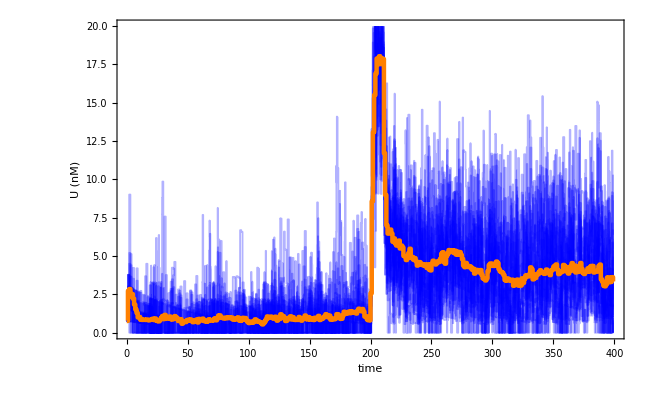

```mathematica
exportGraph=False;
graphSizeCoeff=If[exportGraph,4,1.3];
plotRange={{0,400},{0.,20}};
plotRangePaddingScaled=0.02;
(*Note: The table of raw trajectories simDataAllCellTrajectories contains empty trajectories, which messes up the plotting functions. We have to select the non-zero trajectories in the table before plotting them.*)
plotTimeCourseCellTraj=Show[plotSimCellTraj[U,Select[simDataAllCellTrajectories[[(*Select trajectories at regular intervals in the list of all trajectories*);;;;Round[Length[simDataAllCellTrajectories[[All,3]]]/200]
,3]],Length[#]≠0&],simDataCellsTrajAvg,True,graphSizeCoeff,PlotRange->plotRange]
];
If[!exportGraph,Print[plotTimeCourseCellTraj]];
If[exportGraph,
Export[outputPath<>"/sim_lux02_bR20_bI20_induction_GFP_timecourse_cellTraj_Aexo",plotTimeCourseCellTraj];
];
```

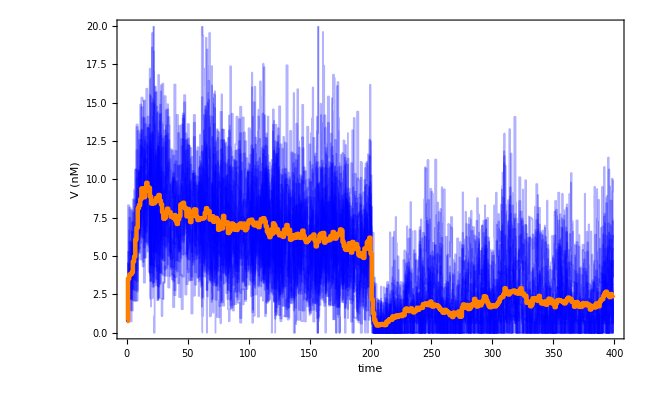

```mathematica
Show[plotSimCellTraj[V,Select[simDataAllCellTrajectories[[(*Select trajectories at regular intervals in the list of all trajectories*);;;;Round[Length[simDataAllCellTrajectories[[All,3]]]/200]
,3]],Length[#]≠0&],simDataCellsTrajAvg,True,graphSizeCoeff,PlotRange->plotRange]
]
```

#### Plot the cell trajectories of cell lineages that survived till the end of the simulation (inverseCellTrajTable)

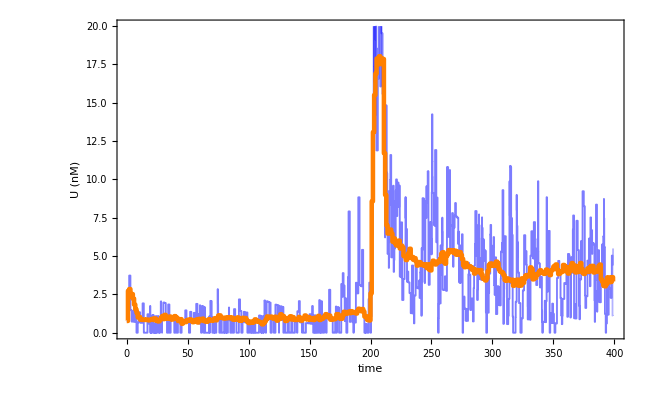

```mathematica
Show[plotSimCellTraj[U,inverseCellTrajTable[[1;;2,All]],simDataCellsTrajAvg,True,graphSizeCoeff,PlotRange->plotRange]]
```

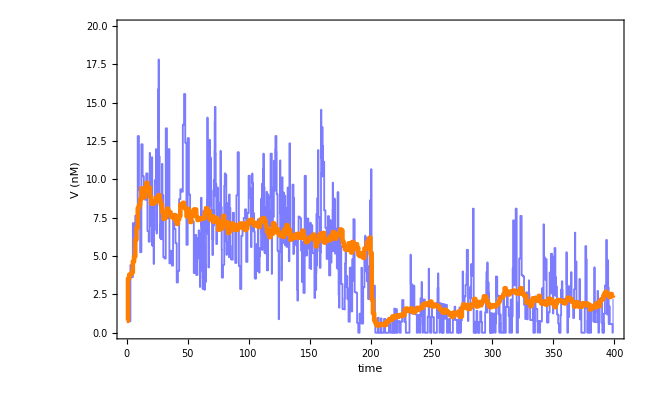

```mathematica
Show[plotSimCellTraj[V,inverseCellTrajTable[[1;;2,All]],simDataCellsTrajAvg,True,graphSizeCoeff,PlotRange->plotRange]]
```

#### Tree plot of all the individual cell trajectories

Extract x positions from the tree plot graph and use them for the custom tree plot below.

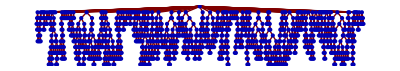

```mathematica
treeplot1=TreePlot[Map[#[[2]]->#[[1]]&,simDataAllCellTrajectories],Top]
xcoordinates=ToExpression[
StringReplace[StringReplace[StringCases[ToString[InputForm[treeplot1]],"VertexCoordinateRules ->"~~__~~"}}",1][[1]],"VertexCoordinateRules ->"->""],{EndOfLine->""," "->""}]
][[2;;-1,1]];
Clear[treeplot1];
```

#### Draw a custom tree plot of all the individual cell trajectories, version 1 constant cell density

```mathematica
treePlotObjects={};
treePlotsimTotalTime=0;
Block[{$RecursionLimit=100,$IterationLimit=6000},
Module[{objects={},childCell,parentCell,drawCellTraj,x,dx,dx0Exp,dx0Lin,totalWidth,t,simTraj=simDataAllCellTrajectories,plotCellTraj,posCellTraj,simTotalTime,initialCellsTraj,speciesColor=U,colorGradient,xScaleFactor=100},

parentCell[cellTraj_]:=If[cellTraj[[2]]>0,simTraj[[cellTraj[[2]]]],{}];
childCell[cellTraj_]:=Select[simTraj,#[[2]]==cellTraj[[1]]&,2];

posCellTraj=Table[{},{i,Length[simTraj]}];
dx0Exp=100;
dx0Lin=10;
dx=10;
totalWidth=200;
simTotalTime=Max[Select[simTraj,Length[#[[3]]]>0&][[All,3,-1,1]]];
Print["simTotalTime = ",simTotalTime];
Print["nb of cell traj = ",Length[simTraj]];

colorGradient[xconc_]:=Module[{colorGradientBase,cmax,cmin},
colorGradientBase[x_]:=Blend[{GrayLevel[0.6],Green},x];
colorGradientBase[x_]:=Blend[{Black,Green,Orange},x];
colorGradientBase[x_]:=Blend[{Black,Green},x];
cmin=0;
cmax=10;
colorGradientBase[Min[Max[(xconc-cmin),0]/(cmax-cmin),1]]
];

plotCellTraj[cellTraj_,x1_,y1_]:=Module[{y2,nSegment=10,dtSegment,segmentList},
If[Length[cellTraj[[3]]]>1,
y2=-cellTraj[[3,-1,1]];
dtSegment=-(y2-y1)/nSegment;
segmentList=Table[
Select[cellTraj[[3]],#[[1]]>iSegment*dtSegment&,1][[1]]
,{iSegment,nSegment-3}];
segmentList=Union[segmentList,SameTest->(#1[[1]]==#2[[1]]&)];
Join[
{{Line[{{x1,y1},{x1,y2}}]}},
{{colorGradient[cellTraj[[3,1,1+nSMilieu+pos[speciesColor,speciesCell]]]],
CapForm["Butt"],Line[{{x1,y1},{x1,-segmentList[[1,1]]}}]
}},
Table[
{colorGradient[segmentList[[iSegment,1+nSMilieu+pos[speciesColor,speciesCell]]]],
CapForm["Butt"],Line[{{x1,-segmentList[[iSegment,1]]},{x1,-segmentList[[iSegment+1,1]]}}]
},{iSegment,Length[segmentList]-1}],
{{colorGradient[cellTraj[[3,-1,1+nSMilieu+pos[speciesColor,speciesCell]]]],
Line[{{x1,-segmentList[[-1,1]]},{x1,-cellTraj[[3,-1,1]]}}]}}
]
(*{Line[{{x1,y1},{x1,y2}}]}*)
,
{}]
];


drawCellTraj[cellTraj_,x1_,y1_]:=Module[{xChild1,xChild2,childCells},

(*objects=Join[objects,plotCellTraj[cellTraj,x1]];*)
objects=Join[objects,plotCellTraj[cellTraj,x1,y1]];
childCells=childCell[cellTraj];
If[Length[childCells]==2 ,
If[ childCells[[1,1]]<Infinity,
(*
xChild1=x1-dx0Exp N[Exp[-4cellTraj[[3,-1,1]]/simTotalTime]];
xChild2=x1+dx0Exp N[Exp[-4cellTraj[[3,-1,1]]/simTotalTime]];
*)
(*
xChild1=x1-dx0Lin(0.5+2*RandomReal[]);
xChild2=x1+dx0Lin(0.5+2*RandomReal[]) ;
*)
xChild1=xScaleFactor*xcoordinates[[childCells[[1,1]]]];
xChild2=xScaleFactor*xcoordinates[[childCells[[2,1]]]];

(*Draw division line*)objects=Join[objects,{CapForm["Square"],colorGradient[cellTraj[[3,-1,1+nSMilieu+pos[speciesColor,speciesCell]]]],Line[{{xChild1,-cellTraj[[3,-1,1]]},{xChild2,-cellTraj[[3,-1,1]]}}]}];
(*Print["xChild1 = ",xChild1," xChild2 = ",xChild2];*)
(*Draw child cells*)
drawCellTraj[childCells[[1]],xChild1,-cellTraj[[3,-1,1]]];
drawCellTraj[childCells[[2]],xChild2,-cellTraj[[3,-1,1]]];
];
];
];

initialCellsTraj=Select[simTraj,Length[parentCell[#]]==0&];

Do[
drawCellTraj[iCell,xScaleFactor*xcoordinates[[iCell[[1]]]],0];
,{iCell,initialCellsTraj}];

treePlotObjects=objects;
treePlotsimTotalTime=simTotalTime;
];
];
```

simTotalTime = 399.

nb of cell traj = 1248

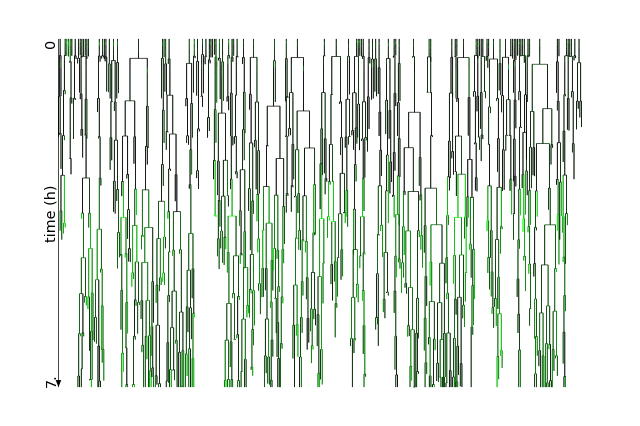

```mathematica
exportGraph=False;
graphSizeCoeff=If[exportGraph,4,0.8];
fontsize=graphSizeCoeff*18;
imagesize=graphSizeCoeff*800;

treePlot=Show[Graphics[
{Thickness[0.0008],
treePlotObjects,
Arrowheads[0.02],Arrow[{Scaled[{-0.015,0},{0,0}],Scaled[{-0.015,0},{0,-treePlotsimTotalTime}]}],
Inset[Style[Text["time (h)"],FontSize->fontsize,FontFamily->fontFamily],Scaled[{-0.02,0},{0,-treePlotsimTotalTime/2}],{Center,Bottom},Automatic,{0,1}],
Inset[Style[Text["0"],FontSize->fontsize,FontFamily->"Arial"],Scaled[{-0.03,0},{0,0}],{Right,Bottom},Automatic,{0,1}],
Inset[Style[ToString[StringForm["``",NumberForm[treePlotsimTotalTime/60,1]]],FontSize->fontsize,FontFamily->fontFamily],Scaled[{-0.03,0},{0,-treePlotsimTotalTime}],{Left,Bottom},Automatic,{0,1}]
}],PlotRangePadding->Scaled[0.01],ImageSize->imagesize,AspectRatio->1/1.5];
If[!exportGraph,Print[treePlot];];
If[exportGraph,
Export[outputPath<>"/lux02_bR20_bI20_plot_sim_induction_GFP_treePlot_"<>StringDrop[filenameSufix,1]<>".png",treePlot];
]
```

#### Draw a custom tree plot of all the individual cell trajectories, version 2 exponential growth

```mathematica
Dimensions[simDataAllCellTrajectories]
```

```mathematica
nCellsFunctionData2=({#,Nearest[simDataXConc[[iTraj,All,3]]->simDataXConc[[iTraj,All,2]],#][[1]]}&/@(Max[Select[simDataAllCellTrajectories,Length[#[[3]]]>0&][[All,3,-1,1]]]*Range[0,1,0.005]));
nCellsFunction2=Interpolation[nCellsFunctionData2];
```

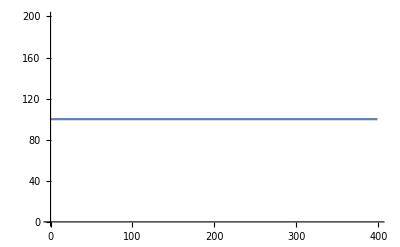

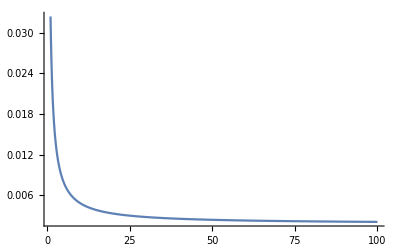

simTotalTime = 399.

nb of cell traj = 1248

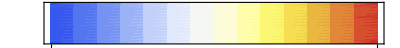

```mathematica
(*treePlotObjects={};
treePlotsimTotalTime=0;*)
Block[{$RecursionLimit=100,$IterationLimit=6000},
Module[{objects={},childCell,parentCell,drawCellTraj,x,dx,dx0Exp,dx0Lin,totalWidth,t,simTraj=simDataAllCellTrajectories,plotCellTraj,posCellTraj,simTotalTime,initialCellsTraj,speciesColor=U,colorGradient,xScaleFactor=100,colorGradientBase,cmax=10,cmin=0,nCellsMax,nCellsFunction,nCellsFunctionData,thicknessFunction},

(*X and Y coordinates are inversed!!!*)

parentCell[cellTraj_]:=If[cellTraj[[2]]>0,simTraj[[cellTraj[[2]]]],{}];
childCell[cellTraj_]:=Select[simTraj,#[[2]]==cellTraj[[1]]&,2];

posCellTraj=Table[{},{i,Length[simTraj]}];
dx0Exp=100;
dx0Lin=10;
dx=10;
totalWidth=300;
simTotalTime=Max[Select[simTraj,Length[#[[3]]]>0&][[All,3,-1,1]]];

(*Find how many cells in the population as a function of time*)
nCellsFunctionData=nCellsFunctionData2;
nCellsFunction=nCellsFunction2;
Print[Plot[nCellsFunction[t],{t,0,simTotalTime}]];
nCellsMax=simDataXConc[[1,-1,2]];
(*thicknessFunction[n_]:=Module[{thick1=0.0015,thick2=4*0.0015},thick2 Exp[(n/nCellsMax)*Log[thick1/thick2]]];*)
thicknessFunction[n_]:=Module[{thick1=0.0018,thick2=18*0.0018},(thick2-thick1)*(1/n)+thick1];
Print[Plot[thicknessFunction[n],{n,1,nCellsMax},PlotRange->All]];
(*Return[];*)

Print["simTotalTime = ",simTotalTime];
Print["nb of cell traj = ",Length[simTraj]];

colorGradientBase[x_]:=Blend[{GrayLevel[0.6],Green},x];
colorGradientBase[x_]:=Blend[{Black,Green,Orange},x];
colorGradientBase[x_]:=Blend[{Black,Green},x];
colorGradientBase=ColorData["TemperatureMap"];
colorGradient[xconc_]:=colorGradientBase[Min[Max[(xconc-cmin),0]/(cmax-cmin),1]];

colorCodePlot=
DensityPlot[z,{z,cmin,cmax},{y,0,10},PlotRange->{cmin,cmax},ColorFunction->Function[z,colorGradientBase[z]],PlotRangePadding->None,PlotRangeClipping->False,AspectRatio->1/25,FrameTicks->{{None,None},{{cmin,cmax},None}}
];
Print[colorCodePlot];

plotCellTraj[cellTraj_,x1_,y1_]:=Module[{y2,nSegment=50,dtSegment,segmentList,nCellsTable},
If[Length[cellTraj[[3]]]>1,

y2=cellTraj[[3,-1,1]];
(*y1=cellTraj[[3,1,1]];*)
(*Print["y1 = ",y1," y2 = ",y2];*)
dtSegment=tau/nSegment//.par;
(*Print["dtSegment = ",dtSegment];*)
(*Print["cellTraj = ",cellTraj[[3,;;;;200]]];*)
segmentList=
Join[
{cellTraj[[3,1]]}
,
If[y2>y1+1*dtSegment,
Reap[
Block[{iSegment=1},
Do[
If[i[[1]]>y1+iSegment*dtSegment,
Sow[i];
iSegment++;
]
,{i,cellTraj[[3]]}]
]
][[2,1]]
,{}]
,
{cellTraj[[3,-1]]}
];
(*Print["segmentList = ",segmentList];*)
segmentList=Union[segmentList,SameTest->(#1[[1]]==#2[[1]]&)];
(*Print["segmentList = ",segmentList];*)

nCellsTable=nCellsFunction/@segmentList[[All,1]];
(*Print[nCellsTable];*)

Join[
{{colorGradient[segmentList[[1,1+pos[speciesColor,speciesCell]]]],Thickness[thicknessFunction[nCellsTable[[2]]]],
CapForm["Square"],Line[{{y1,x1},{segmentList[[2,1]],x1}}]
}},
Table[
{colorGradient[segmentList[[iSegment,1+pos[speciesColor,speciesCell]]]],
CapForm["Butt"],Thickness[thicknessFunction[nCellsTable[[iSegment]]]],Line[{{segmentList[[iSegment,1]],x1},{segmentList[[iSegment+1,1]],x1}}]
},{iSegment,2,Length[segmentList]-1}]
,
{Thickness[thicknessFunction[nCellsTable[[-1]]+1]]}
]
,
{}]
];


drawCellTraj[cellTraj_,x1_,y1_]:=Module[{xChild1,xChild2,childCells},

objects=Join[objects,plotCellTraj[cellTraj,x1,y1]];
childCells=childCell[cellTraj];
If[Length[childCells]==2 ,
If[ childCells[[1,1]]<Infinity,
(*
xChild1=x1-dx0Exp N[Exp[-4cellTraj[[3,-1,1]]/simTotalTime]];
xChild2=x1+dx0Exp N[Exp[-4cellTraj[[3,-1,1]]/simTotalTime]];
*)
(*
xChild1=x1-dx0Lin(0.5+2*RandomReal[]);
xChild2=x1+dx0Lin(0.5+2*RandomReal[]) ;
*)
xChild1=xScaleFactor*xcoordinates[[childCells[[1,1]]]];
xChild2=xScaleFactor*xcoordinates[[childCells[[2,1]]]];

(*Draw division line*)objects=Join[objects,{CapForm["Square"],colorGradient[cellTraj[[3,-1,1+pos[speciesColor,speciesCell]]]],Line[{{cellTraj[[3,-1,1]],xChild1},{cellTraj[[3,-1,1]],xChild2}}]}];
(*Print["xChild1 = ",xChild1," xChild2 = ",xChild2];*)
(*Draw child cells*)
(*If[childCells[[1,1]]≤3,*)
drawCellTraj[childCells[[1]],xChild1,cellTraj[[3,-1,1]]];
drawCellTraj[childCells[[2]],xChild2,cellTraj[[3,-1,1]]];
(*];*)
];
];
];

initialCellsTraj=Select[simTraj,Length[parentCell[#]]==0&];

Do[
drawCellTraj[iCell,xScaleFactor*xcoordinates[[iCell[[1]]]],0];
,{iCell,initialCellsTraj(*simTraj[[150;;150]]*)}];

treePlotObjects=objects;
treePlotsimTotalTime=simTotalTime;
];
];
```

NumberForm::sigz: In addition to the number of digits requested, one or more zeros will appear as placeholders.

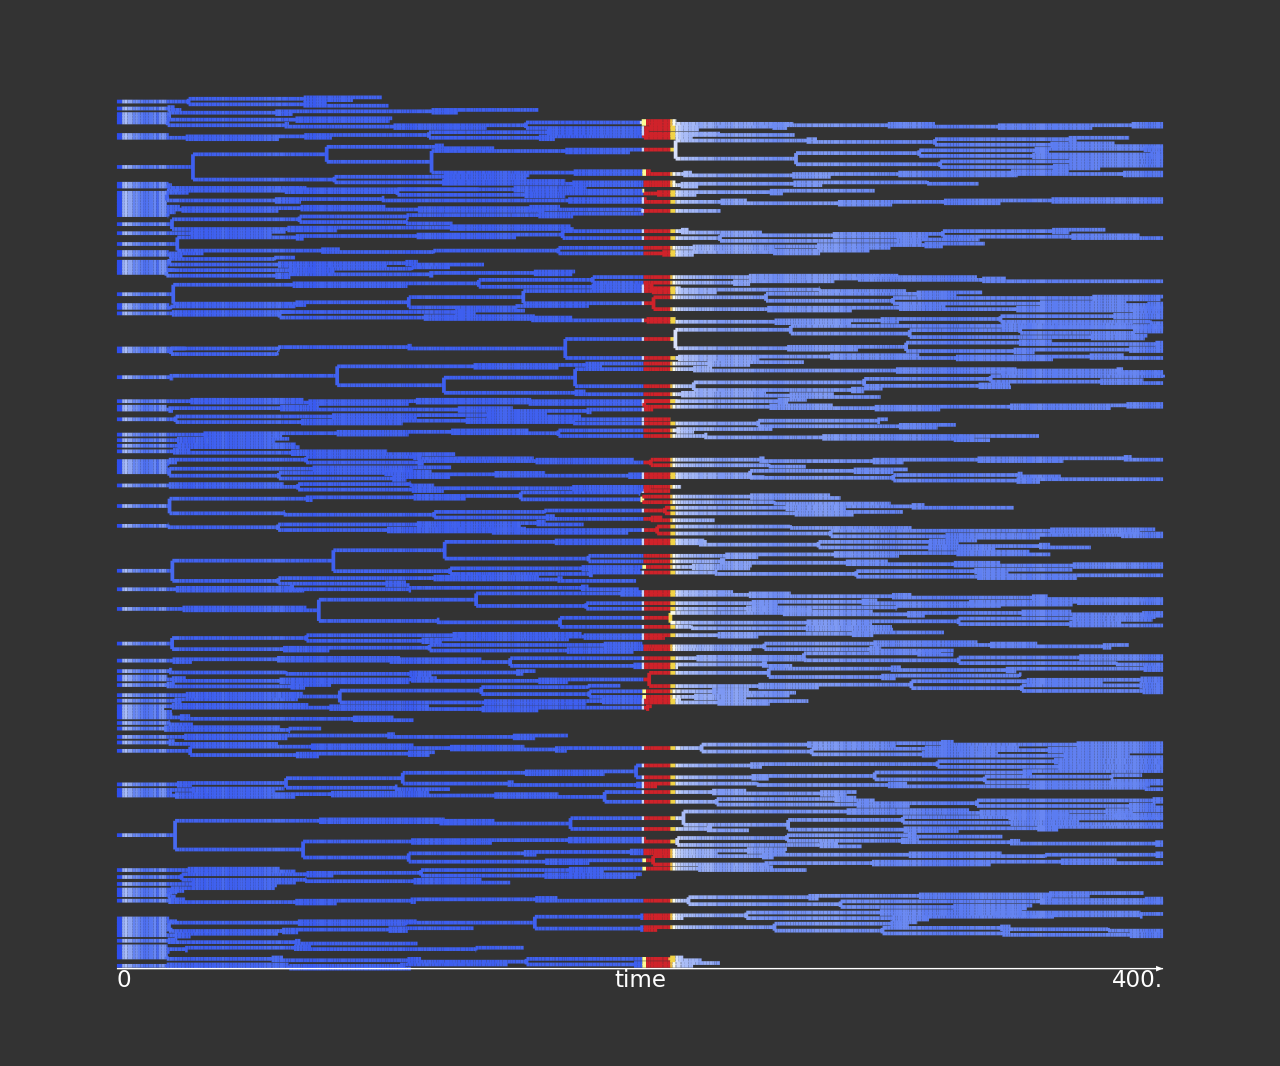
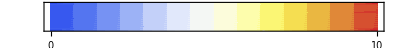

```mathematica
exportGraph=False;
graphSizeCoeff=If[exportGraph,4,2];

treePlot=
Show[Graphics[
{
treePlotObjects
,
White,Arrowheads[0.02],Arrow[{Scaled[{0,-0.015},{0,0}],Scaled[{0,-0.015},{treePlotsimTotalTime,0}]}],
Inset[Style[Text["time"],FontSize->0.8*graphSizeCoeff*fontsize,FontColor->White,FontFamily->fontFamily],Scaled[{0,-0.02},{treePlotsimTotalTime/2,0}],{Center,Top}],
Inset[Style[Text["0"],FontSize->0.8*graphSizeCoeff*fontsize,FontColor->White,FontFamily->fontFamily],Scaled[{0,-0.03},{0,0}],{Left,Top}],
Inset[Style[ToString[StringForm["``",NumberForm[treePlotsimTotalTime,1]]],FontSize->0.8*graphSizeCoeff*fontsize,FontColor->White,FontFamily->fontFamily],Scaled[{0,-0.03},{treePlotsimTotalTime,0}],{Right,Top}]
,
Inset[
Show[colorCodePlot,FrameTicksStyle->Directive[FontFamily->fontFamily,FontColor->White,FontSize->graphSizeCoeff*0.8*fontsize],ImagePadding->graphSizeCoeff*{{5,8},{18,2}}
,Epilog->{
Inset[Style["TraditionalForm`u (nM)",FontFamily->fontFamily,FontColor->White,FontSize->graphSizeCoeff*0.8fontsize],Scaled[{0.5,0}],{Center,Top}]
}]
,{treePlotsimTotalTime/2,100*Max[xcoordinates]},{Center,Bottom},treePlotsimTotalTime/2]

}
],
PlotRangePadding->Scaled[0.01],ImageSize->graphSizeCoeff*imagesize,AspectRatio->1/1.2,Background->GrayLevel[0.2]];
If[!exportGraph,Print[treePlot];];
If[exportGraph,
Export[growingDirectory<>"/exponential_growth.png",treePlot];
]
```

### Movie

#### Color gradient functions

```mathematica
colorGradientBase[x_]:=Blend[{Black,Green},x];
cmax=1;
cmin=0.05;
colorGradientScaling[y_]:=Log[10,Max[y/cmin,1]]/Log[10,cmax/cmin];
colorGradient[xconc_]:=colorGradientBase[colorGradientScaling[xconc]];
Plot[colorGradientScaling[xconc],{xconc,cmin,cmax},AxesOrigin->{0,0},PlotRange->All]

colorGradientScaling[y_]:=(y-cmin)/cmax;
colorGradient[xconc_]:=colorGradientBase[colorGradientScaling[xconc]];
Plot[colorGradientScaling[xconc],{xconc,cmin,cmax},AxesOrigin->{0,0},PlotRange->All]
Graphics[Table[{colorGradient[x],Disk[{x/cmax,0},0.2]},{x,cmin,cmax,0.1}],ImageSize->150]
```

#### Read simulation data

```mathematica
inputPath="example";
iTrajectory=1;
SetDirectory[inputPath];
(*simDataX=Table[Drop[Import["x_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];*)
simDataXConc=Table[Drop[Import["xConc_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,iTrajectory,iTrajectory}];
simCellsVolume=Table[Drop[Import["volumes_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,iTrajectory,iTrajectory}];
simDataAngle=Table[Drop[Import["angle_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,iTrajectory,iTrajectory}];
simDataPosition=Table[Drop[Import["position_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,iTrajectory,iTrajectory}];
simDataLineage=Table[Drop[Import["cell_lineage_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,iTrajectory,iTrajectory}];
```

```mathematica
inputPath2="/home/mweber/DATA/PROGS/OUTPUT/QS_precision2/mutant/lux01_induction/10h/AIxAdded40.000";
nTrajectories=1;
SetDirectory[inputPath2];
simDataXConc2=Table[Drop[Import["xConc_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];
simCellsVolume2=Table[Drop[Import["volumes_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];
simDataAngle2=Table[Drop[Import["angle_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];
simDataPosition2=Table[Drop[Import["position_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];
simDataLineage2=Table[Drop[Import["cell_lineage_traj"<>intstring[iTraj-1]<>".dat","CSV"],-1],{iTraj,nTrajectories}];
```

#### Compute movie

```mathematica
Module[{drawSize,timestep,xx,xxt,xxangle,xxanglet,xxvolumes,xxvolumest,xxconc,xxconct,xxAIxconct,nCells,time,nt,it,drawSuppositoire,xxCellLength,xxtime,simTraj,frame,frameLegend,printLegend,printRequCircle,exportMovie,printAnimate,testRun,cAIxmax,timeStart=350,
simXconc=simDataXConc[[1]],
simVolume=simCellsVolume[[1]],
simAngle=simDataAngle[[1]],
simPosition=simDataPosition[[1]],V00=V0/.par,cellLength0=cellLength0/.par,cellHeight0=cellHeight0/.par,magnifier=1,fieldOfViewSize,magnifierTimeFunction,useMagnifierTimeFunction,
doubleSim,simXconc2,simVolume2,simAngle2,simPosition2,frameDoubleSim,
species,posSpecies,cmax,cmin,colorGradient,colorGradientAIx,colorGradientBase,colorGradientBaseAIx},

testRun=True;
doubleSim=False;
useMagnifierTimeFunction=True;
timeMeshSliceLength=0.01;
drawSize=Round[800,16];(*must be a multiple of 16 for better movie encoding*)
exportMovie=!testRun;
printAnimate=testRun;
printLegend=True;
printRequCircle=False;

species=U;posSpecies=pos[species];
(*Select the time steps which are multiples values of the time mesh. Discard intermediate steps due to cell divisions or cell death.*)
timestep=5*timeMeshSliceLength;
simXconc=Select[simXconc,(FractionalPart[#[[3]]/timestep]<1*^-15)&&#[[3]]>timeStart&];
simVolume=Select[simVolume,(FractionalPart[#[[3]]/timestep]<1*^-15)&&#[[3]]>timeStart&];
simAngle=Select[simAngle,(FractionalPart[#[[3]]/timestep]<1*^-15)&&#[[3]]>timeStart&];
simPosition=Select[simPosition,(FractionalPart[#[[3]]/timestep]<1*^-15)&&#[[3]]>timeStart&];

If[doubleSim,
simXconc2=simDataXConc2[[1]];
simVolume2=simCellsVolume2[[1]];
simAngle2=simDataAngle2[[1]];
simPosition2=simDataPosition2[[1]];
simXconc2=Select[simXconc2,(FractionalPart[#[[3]]/timeMeshSliceLength]<1*^-15)&];
simVolume2=Select[simVolume2,(FractionalPart[#[[3]]/timeMeshSliceLength]<1*^-15)&];
simAngle2=Select[simAngle2,(FractionalPart[#[[3]]/timeMeshSliceLength]<1*^-15)&];
simPosition2=Select[simPosition2,(FractionalPart[#[[3]]/timeMeshSliceLength]<1*^-15)&];
];

nt=Length[simXconc];
Print["nt = ",nt];
xxconct[simXconc_,jt_,iCell_]:=extractX[simXconc,species,jt,iCell];
xxAIxconct[simXconc_,jt_]:=extractAIx[simXconc,jt];
xxt[simPosition_,jt_,iCell_]:=magnifier*(extractPosition[simPosition,jt,iCell]-0.5)+{0.5,0.5};
nCells[simPosition_,jt_]:=(Length[simPosition[[jt]]]-3)/2;
time[simXconc_,jt_]:=extractTime[simXconc,jt];
xxanglet[simAngle_,jt_,iCell_]:=extractAngle[simAngle,jt,iCell];
xxvolumest[simVolume_,jt_,iCell_]:=extractVolume[simVolume,jt,iCell]/V00;

(*PRINT OUT CONCENTRATIONS IN COLOR CODE*)
cmin=0;Print["cmin = ",cmin];
cmax=10;Print["cmax = ",cmax];
(*colorGradientBase=ColorData["AvocadoColors"];*)
colorGradientBase[x_]:=Blend[{GrayLevel[0.6],Green},x];
colorGradientBase[x_]:=Blend[{Black,Green},x];
colorGradient[xconc_]:=
colorGradientBase[Min[Max[(xconc-cmin),0]/(cmax-cmin),1]];
Print[Graphics[Table[{colorGradientBase[x],Disk[{x,0},0.2]},{x,0,1,1/8}],ImageSize->150]];

(*PRINT OUT CONCENTRATION OF AIX IN COLOR CODE FOR THE BACKGROUND*)
cAIxmax=10;Print["cAIxmax = ",cAIxmax];
colorGradientBaseAIx[x_]:=Blend[{Opacity[1,GrayLevel[0.6]],Opacity[1,Lighter[Blue,0.3]]},x];
colorGradientAIx[AIxconc_]:=
colorGradientBaseAIx[Min[AIxconc/cAIxmax,1]];
Print[Graphics[Table[{colorGradientBaseAIx[x],Disk[{x,0},0.2]},{x,0,1,1/8}],ImageSize->150]];

(*FUNCTION TO DRAW THE CELLS*)
drawSuppositoire[x_,l_,h_,θ_,DivisionLine_,color_,divisionColorBorder_]:=
Module[{output,pts,nPointsCircle,polygon,line},
nPointsCircle=16;
pts=Join[{{-(l-h)/2,h/2},{(l-h)/2,h/2}},
Table[{(l-h)/2,0}+{(h/2)Cos[angle],(h/2)Sin[angle]},{angle,Pi/2,-Pi/2,-Pi/nPointsCircle}],
{{(l-h)/2,-h/2},{-(l-h)/2,-h/2}},
Table[{-(l-h)/2,0}+{(h/2)Cos[angle],(h/2)Sin[angle]},{angle,3Pi/2,Pi/2,-Pi/nPointsCircle}]];
polygon=Translate[Rotate[Polygon[pts],π θ/180,{0,0}],x];
line=Translate[Rotate[Line[{{0,-h/2},{0,h/2}}],π θ/180,{0,0}],x];
output={color,EdgeForm[{GrayLevel[0.7],Thickness[0.04]}],polygon};
If[DivisionLine,output={color,EdgeForm[{divisionColorBorder,Thick}],polygon,divisionColorBorder,Thick,line}];
output
];

Print[Graphics[drawSuppositoire[xxt[simPosition,1,1],cellLength0*xxvolumest[simVolume,1,1]/V00,cellHeight0,xxanglet[simAngle,1,1],False,colorGradient[xxconct[simXconc,1,1]],Red]]];


(*DRAWING THE FRAMES*)
frameLegend=Panel[Row[{
Column[{Style[ToString[species]<>"(t) (nM)",FontSize->30*drawSize/1000],
Rasterize[ParametricPlot[{x,y},{x,cmin,cmax},{y,0,1},Mesh->None,ColorFunction->(colorGradientBase[#]&),Frame->{True,False,False,False},FrameTicks->{{None,None},{{0,Round[cmax]},None}},FrameTicksStyle->Directive[FontSize->30*drawSize/1000],AspectRatio->0.2,ImageSize->200*drawSize/1000,Background->LightGray],Background->LightGray]
}],
Column[{Style["AIx(t) (nM)",FontSize->30*drawSize/1000],
Rasterize[ParametricPlot[{x,y},{x,0,cAIxmax},{y,0,1},Mesh->None,ColorFunction->(colorGradientBaseAIx[#]&),Frame->{True,False,False,False},FrameTicks->{{None,None},{{0,cAIxmax},None}},FrameTicksStyle->Directive[FontSize->30*drawSize/1000],AspectRatio->0.2,ImageSize->200*drawSize/1000,Background->LightGray],Background->LightGray]
}]
},"   "]];
Print[frameLegend];

(*Calculate initial field of view size as the final radius of the colony*)
fieldOfViewSize=2*1.2*N[Sqrt[(nCells[simPosition,-1]*cellLength0/Log[2]*cellHeight0)/Pi]];

magnifierTimeFunction[jt_]:=Module[{zoomValuesTable={{1.6,0},{1.1,0.25},{1.1,1},{1.1,1.1}},transitionTime=50/nt,piecewiseTable},
piecewiseTable={};
Do[
piecewiseTable=Join[piecewiseTable,{{zoomValuesTable[[iStep-1,1]],zoomValuesTable[[iStep-1,2]]<jjt≤zoomValuesTable[[iStep,2]]-transitionTime},
{zoomValuesTable[[iStep-1,1]]-(zoomValuesTable[[iStep-1,1]]-zoomValuesTable[[iStep,1]])/transitionTime(jjt-(zoomValuesTable[[iStep,2]]-transitionTime)),zoomValuesTable[[iStep,2]]-transitionTime<jjt≤zoomValuesTable[[iStep,2]]}}];
,{iStep,2,Length[zoomValuesTable]}];
Piecewise[piecewiseTable//.jjt->jt]
];
Print["Magnifier (zoom) function:\n",Plot[magnifierTimeFunction[jt],{jt,0,1},ImageSize->200]];

frame[jt_]:=Module[{jjt=If[jt<0,nt-jt,jt]},
Style[Graphics[{
{colorGradientAIx[xxAIxconct[simXconc,jt]],Disk[{0,0},0.55]},
Scale[
Table[{
If[(*Norm[xxt[simPosition,jt,iCell]-{0,0}]*)0<fieldOfViewSize/2+cellLength0,
{drawSuppositoire[xxt[simPosition,jt,iCell],cellLength0*xxvolumest[simVolume,jt,iCell],cellHeight0,xxanglet[simAngle,jt,iCell],False,colorGradient[xxconct[simXconc,jt,iCell]],Red]},{}]
}
,{iCell,nCells[simPosition,jt]}]
,1/fieldOfViewSize*If[useMagnifierTimeFunction,magnifierTimeFunction[jjt/nt],1],{0,0}]
(*,Inset[Panel[Row[Style[#,FontSize->30*drawSize/1000]&/@{"time ",PaddedForm[time[simXconc,jt]/60,{4,1},NumberPadding->{" ","0"}]," (h)"}]],{-0.58,0.58},{Left,Top}]*)
(*,
If[printLegend,Inset[frameLegend,{0.58,0.58},{Right,Top}],{}]
*)},
PlotRangePadding->0,ImageSize->drawSize,PlotRange->{{-0.6,0.6},{-0.6,0.6}},Background->colorGradientAIx[0]],Antialiasing->True]];

frameDoubleSim[jt_]:=Style[Graphics[{
{colorGradientAIx[xxAIxconct[simXconc,jt]],Disk[{0.5,0.5},0.55]},
Table[{
If[Norm[xxt[simPosition,jt,iCell]-{0.5,0.5}]<0.5+cellLength,
{drawSuppositoire[xxt[simPosition,jt,iCell],cellLength*xxvolumest[simVolume,jt,iCell],cellHeight,xxanglet[simAngle,jt,iCell],False,colorGradient[xxconct[simXconc,jt,iCell]],Red]},{}]
}
,{iCell,nCells[simPosition,jt]}],

{colorGradientAIx[xxAIxconct[simXconc2,jt]],Disk[{1.65,0.5},0.55]},
Table[{
If[Norm[xxt[simPosition2,jt,iCell]-{0.5,0.5}]<0.5+cellLength,
{drawSuppositoire[xxt[simPosition2,jt,iCell]+{1.15,0},cellLength*xxvolumest[simVolume2,jt,iCell],cellHeight,xxanglet[simAngle2,jt,iCell],False,colorGradient[xxconct[simXconc2,jt,iCell]],Red]},{}]
}
,{iCell,nCells[simPosition2,jt]}],

Inset[
Text[Style["Wild type",FontSize->60*drawSize/1000,Bold,FontColor->Yellow,Opacity[Piecewise[{{1/tfade jt,jt<tfade},{1,jt<tfade+tstay},{1-1/tfade(jt-tfade-tstay),jt<2tfade+tstay}},0]/.{tfade->50,tstay->100}]
]],{0.5,0.8},{Center,Top}],

Inset[
Text[Style["Mutant",FontSize->60*drawSize/1000,Bold,FontColor->Yellow,
Opacity[Piecewise[{{1/tfade jt,jt<tfade},{1,jt<tfade+tstay},{1-1/tfade(jt-tfade-tstay),jt<2tfade+tstay}},0]/.{tfade->50,tstay->100}]
]],{1.65,0.8},{Center,Top}
],

Inset[Panel[Row[Style[#,FontSize->30*drawSize/1000]&/@{"time ",PaddedForm[time[simXconc,jt]/60,{4,1},NumberPadding->{" ","0"}]," (h)"}]],Scaled[{0.02,0.98}],{Left,Top}],
If[printLegend,Inset[frameLegend,Scaled[{0.98,0.98}],{Right,Top}],{}]
},PlotRangePadding->0,ImageSize->{Automatic,drawSize},PlotRange->{{-0.1,2.25},{-0.1,1.1}},Background->colorGradientAIx[0]],Antialiasing->True];


(*EXPORTING IMAGES*)
If[exportMovie,
Module[{fileNameTable},
CreateDirectory[inputPath<>"/movie/png"];
SetDirectory[inputPath<>"/movie/png"];
DeleteFile[FileNames["*.png"]];
fileNameTable=Table["image"<>StringDrop[ToString[PaddedForm[jt,4,NumberPadding->{"0",""}]],{1,1}]<>".png",{jt,1,nt+1}];
Do[
Export[fileNameTable[[jt]],
Style[
If[doubleSim,
frameDoubleSim[jt],
frame[jt]]
,Antialiasing->True]
,ImageSize->{Automatic,drawSize},"CompressionLevel"->0,ColorSpace->RGBColor,Background->White];Print[jt," /",nt];
,{jt,1,nt,1}];
];
Print["Images exported."];
];

If[printAnimate,
If[doubleSim,
Print[frameDoubleSim[30]];
Print[frameDoubleSim[-1]];
,
Do[
Print[frame[Max[1,Ceiling[i*nt]]]];
,{i,0,1,0.05}]
];
];

(*ANIMATION*)
(*
If[printAnimate,
Print[Animate[
frame[jt]
,{jt,1,10,1},AnimationRepetitions->1,AnimationRunning->True,DisplayAllSteps->True]]
];
*)
]
```